# 0 | General definitions and assumptions

### A priori assumptions

```mathematica
pO=1-2pAB;
pO=1-pA-pB;
pOr=1-pAr-pBr-pOR-pAR-pBR;
```

```mathematica
0≤(m1+m2)≤1
0≤m1≤1-m2
0≤m2≤1-m1
```

### Mainland population stable cytotype frequencies

As per Turelli (1994):

```mathematica
beta[t_,l_]:=1/(2t)+1/(2t)√(1-(4(1-t)t)/l);
```

### Analytical assumptions

```mathematica
Clear[t,l] (* Housekeeping *)
```

It follows from the definition of β above that the following must be true for β ∈ ℝ, β ∈ {0, 1} and t, l ∈ {0, 1}:

```mathematica
4 t-4 t^2≤l≤1;
1/2+(√(1-l))/2≤t≤1;
```

Justification :

```mathematica
Reduce[{1/(2t)+1/(2t)√(1-(4(1-t)t)/l)≥0,1/(2t)+1/(2t)√(1-(4(1-t)t)/l)≤1,t≥0,l≥0,t≤1,l≤1},l]
Reduce[{1/(2t)+1/(2t)√(1-(4(1-t)t)/l)≥0,1/(2t)+1/(2t)√(1-(4(1-t)t)/l)≤1,t≥0,l≥0,t≤1,l≤1},t]
```

(t==1/2&&l==1)||(1/2<t<1&&4 t-4 t^2≤l≤1)||(t==1&&0<l≤1)

0<l≤1&&1/2+(√(1-l))/2≤t≤1

In the special cases where t and/or l = 1, we get :

```mathematica
Reduce[{4 t-4 t^2≤l≤1,t==1},l]
```

t==1&&0≤l≤1

```mathematica
Reduce[{4 t-4 t^2≤l≤1,l==1},t]
```

t∈ℝ&&l==1

```mathematica
Reduce[{1/2+(√(1-l))/2≤t≤1,t==1},l]
```

t==1&&0≤l≤1

```mathematica
Reduce[{1/2+(√(1-l))/2≤t≤1,l==1},t]
```

l==1&&1/2≤t≤1

And in those cases, we additionally have β = 1:

```mathematica
FullSimplify[{beta[1,1],beta[t,1],beta[1,l]},Assumptions->1/2+(√(1-l))/2≤t≤1]
```

{1,1,1}

### Cytotype colours (for plotting)

```mathematica
cytotypeColours={RGBColor[0.286, 0.573, 0.447], RGBColor[0.541, 0.271, 0.541], RGBColor[0.831, 0.729, 0.416]};
```

# 1 | Symmetric migration model without genotypes

In this first and very simplified model we assume the infected cytotypes A and B are always symmetrical, so one equation defines both their frequences. By extension, this also defines the frequency of pO.

## Defining the model

### Step 1 : Migration

```mathematica
pMigrationSymmetric[pAB_,m_,β_]:=(1-2m)pAB+m β;
```

### Step 2 : Selection

```mathematica
pSelectionSymmetric[pmAB_]:=pmAB;
```

### Step 3 : Reproduction

```mathematica
pNextSymmetric[psAB_,t_,l_]:=(psAB t(1-psAB l))/(2 psAB^2 t l-2psAB l+1);
```

#### Derivation of Step 3

```mathematica
Clear[psO,psAB,t,l];(* Housekeeping *)
psO=1-2psAB;(* Simplifying assumption *)
```

All possible crosses generating offspring of type O and offspring of type AB:

```mathematica
pONextSymmetric[pO_,pAB_,t_,l_]:=(pO*pO)(1*1)+(pO*pAB)(1*(1-l))+(pO*pAB)(1*(1-l))+2*((pAB*pO)((1-t)*1)+(pAB*pAB)((1-t)*(1-l))+(pAB*pAB)((1-t)*(1-l)));
pABNextSymmetric[pO_,pAB_,t_,l_]:=(pAB*pO)(t*1)+(pAB*pAB)((t)*1)+(pAB*pAB)((t)*(1-l));
```

```mathematica
FullSimplify[pONextSymmetric[psO,psAB,t,l]]
FullSimplify[pABNextSymmetric[psO,psAB,t,l]]
```

(-1+2 l psAB) (-1+2 psAB t)

psAB (1-l psAB) t

Total mean fitness:

```mathematica
FullSimplify[(-1+2 l psAB) (-1+2 psAB t)+2psAB (1-l psAB) t]
```

1+2 l psAB (-1+psAB t)

```mathematica
FullSimplify[2 psAB^2 t l-2psAB l+1==1+2 l psAB (-1+psAB t)]
```

True

### Complete recursion equation

```mathematica
pRecursionSymmetric[pAB_,m_,t_,l_,β_]:=-((1+(-1+2 m) pAB l- m l β)((-1+2 m) pAB t-m t β))/(1+2((-1+2 m) pAB l-m l β)(1+(-1+2 m) pAB t-m t β));
```

#### Derivation of complete recursion equation

```mathematica
Clear[pO,pAB,m,t,l,β]; (* Housekeeping *)
```

Assumptions :

```mathematica
pO=1-2pAB;
0≤t≤1;
0≤l≤1;
{t,l,pO,pAB}∈ Reals;
```

Simplifying the full expression from its components:

```mathematica
FullSimplify[pNextSymmetric[pSelectionSymmetric[pMigrationSymmetric[pAB,m,β]],t,l]]
```

(t (pAB-2 m pAB+m β) (1+l (-1+2 m) pAB-l m β))/(1-2 l (pAB-2 m pAB+m β)+2 l t (pAB-2 m pAB+m β)^2)

```mathematica
FullSimplify[(t (pAB-2 m pAB+m β) (1+l (-1+2 m) pAB-l m β))/(1-2 l (pAB-2 m pAB+m β)+2 l t (pAB-2 m pAB+m β)^2)==-(t ((-1+2 m) pAB-m β) (1+l (-1+2 m) pAB-l m β))/(1+2 l ((-1+2 m) pAB-m β) (1+(-1+2 m) pAB t-m t β))]
```

True

## Analytical solutions

We try to solve the the general case of this recursion equation analytically to see whether it is possible to find analytical general case equilibria.

### General case

##### Fixed point analysis

```mathematica
Clear[pAB,m,t,l,β]; (* Housekeeping *)
fixedPoints={pAB}/.Simplify[Solve[pRecursionSymmetric[pAB,m,t,l,β]==pAB,pAB]]
```

{{-1/(6 l (1-2 m)^2 t)(-2 l+4 l m+l t-4 l m t+4 l m^2 t+4 l m t β-8 l m^2 t β+(l (1-2 m)^2 (-6 t (1+(-1+2 m) t)+l (4-4 t (1+m (-2+β))+(t-2 m t (1+β))^2)))/(-9 l^2 (-1+2 m)^3 t (2+t (-3+m (6-4 β))+(-1+2 m) t^2 (-1+2 m (1+β)))+l^3 (-1+2 m)^3 (8-12 t (1+m (-2+β))+t^3 (-1+2 m (1+β))^3-6 t^2 (-1+m (4+β)+2 m^2 (-2-β+β^2)))+3 √3 √(-l^3 (1-2 m)^6 t^2 (-8 t (1+(-1+2 m) t)^3+4 l^3 m^2 β^2 (4+t (-4-8 m (-1+β))+(t-2 m t (1+β))^2)-4 l^2 m β (4+2 m t^3 β (1-2 m (1+β))^2+4 t (-1+m (2+β))+t^2 (1-2 m (2+9 β)+m^2 (4+36 β-16 β^2)))+l (4+(1-2 m)^2 t^4 (1-2 m (1+β))^2+4 t (-3+m (6+8 β))+t^2 (13-4 m (13+8 β)+m^2 (52+64 β-32 β^2))+2 (-1+2 m) t^3 (3-2 m (6+β)+4 m^2 (3+β+10 β^2))))))^(1/3)+(-9 l^2 (-1+2 m)^3 t (2+t (-3+m (6-4 β))+(-1+2 m) t^2 (-1+2 m (1+β)))+l^3 (-1+2 m)^3 (8-12 t (1+m (-2+β))+t^3 (-1+2 m (1+β))^3-6 t^2 (-1+m (4+β)+2 m^2 (-2-β+β^2)))+3 √3 √(-l^3 (1-2 m)^6 t^2 (-8 t (1+(-1+2 m) t)^3+4 l^3 m^2 β^2 (4+t (-4-8 m (-1+β))+(t-2 m t (1+β))^2)-4 l^2 m β (4+2 m t^3 β (1-2 m (1+β))^2+4 t (-1+m (2+β))+t^2 (1-2 m (2+9 β)+m^2 (4+36 β-16 β^2)))+l (4+(1-2 m)^2 t^4 (1-2 m (1+β))^2+4 t (-3+m (6+8 β))+t^2 (13-4 m (13+8 β)+m^2 (52+64 β-32 β^2))+2 (-1+2 m) t^3 (3-2 m (6+β)+4 m^2 (3+β+10 β^2))))))^(1/3))},{1/(24 l (1-2 m)^2 t)(4 l (-1+2 m) (-2+t+m t (-2+4 β))+(2 (1+ⅈ √3) l (1-2 m)^2 (-6 t (1+(-1+2 m) t)+l (4-4 t (1+m (-2+β))+(t-2 m t (1+β))^2)))/(-9 l^2 (-1+2 m)^3 t (2+t (-3+m (6-4 β))+(-1+2 m) t^2 (-1+2 m (1+β)))+l^3 (-1+2 m)^3 (8-12 t (1+m (-2+β))+t^3 (-1+2 m (1+β))^3-6 t^2 (-1+m (4+β)+2 m^2 (-2-β+β^2)))+3 √3 √(-l^3 (1-2 m)^6 t^2 (-8 t (1+(-1+2 m) t)^3+4 l^3 m^2 β^2 (4+t (-4-8 m (-1+β))+(t-2 m t (1+β))^2)-4 l^2 m β (4+2 m t^3 β (1-2 m (1+β))^2+4 t (-1+m (2+β))+t^2 (1-2 m (2+9 β)+m^2 (4+36 β-16 β^2)))+l (4+(1-2 m)^2 t^4 (1-2 m (1+β))^2+4 t (-3+m (6+8 β))+t^2 (13-4 m (13+8 β)+m^2 (52+64 β-32 β^2))+2 (-1+2 m) t^3 (3-2 m (6+β)+4 m^2 (3+β+10 β^2))))))^(1/3)+2 (1-ⅈ √3) (-9 l^2 (-1+2 m)^3 t (2+t (-3+m (6-4 β))+(-1+2 m) t^2 (-1+2 m (1+β)))+l^3 (-1+2 m)^3 (8-12 t (1+m (-2+β))+t^3 (-1+2 m (1+β))^3-6 t^2 (-1+m (4+β)+2 m^2 (-2-β+β^2)))+3 √3 √(-l^3 (1-2 m)^6 t^2 (-8 t (1+(-1+2 m) t)^3+4 l^3 m^2 β^2 (4+t (-4-8 m (-1+β))+(t-2 m t (1+β))^2)-4 l^2 m β (4+2 m t^3 β (1-2 m (1+β))^2+4 t (-1+m (2+β))+t^2 (1-2 m (2+9 β)+m^2 (4+36 β-16 β^2)))+l (4+(1-2 m)^2 t^4 (1-2 m (1+β))^2+4 t (-3+m (6+8 β))+t^2 (13-4 m (13+8 β)+m^2 (52+64 β-32 β^2))+2 (-1+2 m) t^3 (3-2 m (6+β)+4 m^2 (3+β+10 β^2))))))^(1/3))},{1/(24 l (1-2 m)^2 t)(4 l (-1+2 m) (-2+t+m t (-2+4 β))+(2 (1-ⅈ √3) l (1-2 m)^2 (-6 t (1+(-1+2 m) t)+l (4-4 t (1+m (-2+β))+(t-2 m t (1+β))^2)))/(-9 l^2 (-1+2 m)^3 t (2+t (-3+m (6-4 β))+(-1+2 m) t^2 (-1+2 m (1+β)))+l^3 (-1+2 m)^3 (8-12 t (1+m (-2+β))+t^3 (-1+2 m (1+β))^3-6 t^2 (-1+m (4+β)+2 m^2 (-2-β+β^2)))+3 √3 √(-l^3 (1-2 m)^6 t^2 (-8 t (1+(-1+2 m) t)^3+4 l^3 m^2 β^2 (4+t (-4-8 m (-1+β))+(t-2 m t (1+β))^2)-4 l^2 m β (4+2 m t^3 β (1-2 m (1+β))^2+4 t (-1+m (2+β))+t^2 (1-2 m (2+9 β)+m^2 (4+36 β-16 β^2)))+l (4+(1-2 m)^2 t^4 (1-2 m (1+β))^2+4 t (-3+m (6+8 β))+t^2 (13-4 m (13+8 β)+m^2 (52+64 β-32 β^2))+2 (-1+2 m) t^3 (3-2 m (6+β)+4 m^2 (3+β+10 β^2))))))^(1/3)+2 (1+ⅈ √3) (-9 l^2 (-1+2 m)^3 t (2+t (-3+m (6-4 β))+(-1+2 m) t^2 (-1+2 m (1+β)))+l^3 (-1+2 m)^3 (8-12 t (1+m (-2+β))+t^3 (-1+2 m (1+β))^3-6 t^2 (-1+m (4+β)+2 m^2 (-2-β+β^2)))+3 √3 √(-l^3 (1-2 m)^6 t^2 (-8 t (1+(-1+2 m) t)^3+4 l^3 m^2 β^2 (4+t (-4-8 m (-1+β))+(t-2 m t (1+β))^2)-4 l^2 m β (4+2 m t^3 β (1-2 m (1+β))^2+4 t (-1+m (2+β))+t^2 (1-2 m (2+9 β)+m^2 (4+36 β-16 β^2)))+l (4+(1-2 m)^2 t^4 (1-2 m (1+β))^2+4 t (-3+m (6+8 β))+t^2 (13-4 m (13+8 β)+m^2 (52+64 β-32 β^2))+2 (-1+2 m) t^3 (3-2 m (6+β)+4 m^2 (3+β+10 β^2))))))^(1/3))}}

Clearly, the general case is not amenable to analytical study for this version of the model (or any more complex implementation). Instead, we will investigate some special cases of more complex model iterations below.

# 2 | Asymmetric migration model without genotypes

In this version of the model, we introduce asymmetry between the CIM strains but not yet a resistance allele. Therefore we require one equation per cytotype.

## Defining the model

### Step 1 : Migration

```mathematica
pMigrationSimple[{pO_,pA_,pB_},m1_,m2_,β_]:={
(1-(m1+m2))pO+(m1+m2)(1-β),
(1-(m1+m2))pA+m1 β,
(1-(m1+m2))pB+m2 β
};
```

### Step 2 : Selection

```mathematica
pSelectionSimple[{pmO_,pmA_,pmB_}]:={pmO/(pmO+pmA+pmB),pmA/(pmO+pmA+pmB),pmB/(pmO+pmA+pmB)};
```

### Step 3 : Reproduction

```mathematica
pNextSimple[{psO_,psA_,psB_},t_,l_]:={((l (psA+psB)-1) (t(psA+psB)-1))/((psA^2+psB^2)t l-(psA+psB)l +1),(t psA (1-l psB))/((psA^2+psB^2)t l-(psA+psB)l +1),(t psB(1-l psA))/((psA^2+psB^2)t l-(psA+psB)l +1)};
```

#### Derivation of Step 3: Reproduction

First, we simplify the expression for mean fitness assuming pO = 1 - pA - pB:

```mathematica
psO=1-psA-psB;
```

```mathematica
FullSimplify[(psO psO)+(psO(1-l)psA)+(psO (1-l)psB)+((1-t)psA psO)+((1-t)psA (1-l)psA)+((1-t)psA (1-l)psB)+((1-t)psB psO)+((1-t)psB (1-l)psA)+((1-t)psB (1-l)psB)+(t psA psO)+(t psA psA)+(t psA (1-l)psB)+(t psB psO)+(t psB(1-l)psA)+(t psB psB)]
```

1-l (psA+psB)+l (psA^2+psB^2) t

Knowing the above, we can simplify the full expressions for the frequencies in the next generation. Again, assuming pO = 1 - pA - pB:

```mathematica
FullSimplify[{((psO psO)+(psO(1-l)psA)+(psO (1-l)psB)+((1-t)psA psO)+((1-t)psA (1-l)psA)+((1-t)psA (1-l)psB)+((1-t)psB psO)+((1-t)psB (1-l)psA)+((1-t)psB (1-l)psB))/(1-l (psA+psB)+l (psA^2+psB^2) t),
((t psA psO)+(t psA psA)+(t psA (1-l)psB))/(1-l (psA+psB)+l (psA^2+psB^2) t),((t psB psO)+(t psB(1-l)psA)+(t psB psB))/(1-l (psA+psB)+l (psA^2+psB^2) t)}]
```

{((-1+l (psA+psB)) (-1+(psA+psB) t))/(1-l (psA+psB)+l (psA^2+psB^2) t),(psA (1-l psB) t)/(1-l (psA+psB)+l (psA^2+psB^2) t),((1-l psA) psB t)/(1-l (psA+psB)+l (psA^2+psB^2) t)}

Then, with minor manual adjustments, we define pNext as above.

## Analytical solutions

We know from the symmetric model that the general case is not amenable to analytical study, so we pursue only special cases here. Other special cases attempted other than those below were (for practical purposes) incomputable or not amenable to analytical study.

### Special case: m_1 = m_2; t = l = 1

#### Fixed point analysis

```mathematica
Clear[psO,pmO,pO,psA,pmA,pA,psB,pmB,pB,m,m1,m2,t,l,β];
```

```mathematica
fixedPoints={pO,pA,pB}/.FullSimplify[Solve[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},m,m,beta[1,1]]],1,1]=={pO,pA,pB},{pO,pA,pB}],Assumptions->{0≤2m≤1,{pO,pA,pB,m,t,l}∈ Reals}]
```

{{0,1/2,1/2},{1-(2 √((-1+m) m))/(-1+2 m),(√((-1+m) m))/(-1+2 m),(√((-1+m) m))/(-1+2 m)},{1+(2 √((-1+m) m))/(-1+2 m),(√((-1+m) m))/(1-2 m),(√((-1+m) m))/(1-2 m)},{0,(-1+√(1-4 m)+2 m)/(-2+4 m),(1+√(1-4 m)-2 m)/(2-4 m)},{0,(1+√(1-4 m)-2 m)/(2-4 m),(-1+√(1-4 m)+2 m)/(-2+4 m)},{1/(1-2 m),(√-m+m)/(-1+2 m),(-ⅈ √m+m)/(-1+2 m)},{1/(1-2 m),(-ⅈ √m+m)/(-1+2 m),(√-m+m)/(-1+2 m)}}

We can tell that some of these equilibria are complex, so for convenience of presentation below we record the index of the Real fixed points:

```mathematica
realFixedPointsIndex={1,2,3,4,5};
```

#### Stability analysis

```mathematica
Jacob[{pO_,pA_,pB_}]=FullSimplify[D[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},m,m,beta[1,1]]],1,1],{{pO,pA,pB}}],Assumptions->{0≤2m≤1,{pO,pA,pB,m,t,l}∈ Reals}];
```

```mathematica
For[i=1,i≤Length[realFixedPointsIndex],i++,
Print[MatrixForm[FullSimplify[Jacob[fixedPoints⟦realFixedPointsIndex[[i]]⟧],Assumptions->{0≤2m≤1,{pO,pA,pB,m,t,l}∈ Reals}]]];
Print[FullSimplify[Eigenvalues[Jacob[fixedPoints⟦realFixedPointsIndex[[i]]⟧]],Assumptions->{0≤2m≤1,{pO,pA,pB,m,t,l}∈ Reals}]];
];
```

(0 | 0 | 0
0 | 1-2 m | -1+2 m
0 | -1+2 m | 1-2 m)

{2-4 m,0,0}

((2 (m+√((-1+m) m)))/(-1+2 m) | 1/(-1+2 m) | 1/(-1+2 m)
-(m+√((-1+m) m))/(-1+2 m) | 1/2 (1+1/(1-2 m)-2 m-2 √((-1+m) m)) | -1/2+1/(2-4 m)+m+√((-1+m) m)
-(m+√((-1+m) m))/(-1+2 m) | -1/2+1/(2-4 m)+m+√((-1+m) m) | 1/2 (1+1/(1-2 m)-2 m-2 √((-1+m) m)))

{0,-1/(-1-2 √((-1+m) m)+m (3-2 m+2 √((-1+m) m)+√(1+4 √((-1+m) m)+8 m (-1+m-√((-1+m) m))))),1/(1+2 √((-1+m) m)+m (-3+2 m-2 √((-1+m) m)+√(1+4 √((-1+m) m)+8 m (-1+m-√((-1+m) m)))))}

((2 (m-√((-1+m) m)))/(-1+2 m) | 1/(-1+2 m) | 1/(-1+2 m)
(-m+√((-1+m) m))/(-1+2 m) | 1/2+1/(2-4 m)-m+√((-1+m) m) | -1/2+1/(2-4 m)+m-√((-1+m) m)
(-m+√((-1+m) m))/(-1+2 m) | -1/2+1/(2-4 m)+m-√((-1+m) m) | 1/2+1/(2-4 m)-m+√((-1+m) m))

{0,1/(1-2 √((-1+m) m)+m (-3+2 m+2 √((-1+m) m)-√(1-4 √((-1+m) m)+8 m (-1+m+√((-1+m) m))))),1/(1-2 √((-1+m) m)+m (-3+2 m+2 √((-1+m) m)+√(1-4 √((-1+m) m)+8 m (-1+m+√((-1+m) m)))))}

(0 | 0 | 0
(√(1-4 m) m)/(1-2 m) | ((1+√(1-4 m)) m)/(1-2 m) | -((-1+√(1-4 m)) m)/(-1+2 m)
(√(1-4 m) m)/(-1+2 m) | ((1+√(1-4 m)) m)/(-1+2 m) | ((-1+√(1-4 m)) m)/(-1+2 m))

{(2 m)/(1-2 m),0,0}

(0 | 0 | 0
(√(1-4 m) m)/(-1+2 m) | ((-1+√(1-4 m)) m)/(-1+2 m) | ((1+√(1-4 m)) m)/(-1+2 m)
(√(1-4 m) m)/(1-2 m) | -((-1+√(1-4 m)) m)/(-1+2 m) | ((1+√(1-4 m)) m)/(1-2 m))

{(2 m)/(1-2 m),0,0}

We solve all the leading eigenvalues for m:

```mathematica
Reduce[0≤2-4 m≤1,m]
```

1/4≤m≤1/2

```mathematica
Reduce[0≤1/(1+2 √((-1+m) m)+m (-3+2 m-2 √((-1+m) m)+√(1+4 √((-1+m) m)+8 m (-1+m-√((-1+m) m)))))≤1,m]
```

m≤0||m==1

```mathematica
Reduce[0≤1/(1-2 √((-1+m) m)+m (-3+2 m+2 √((-1+m) m)+√(1-4 √((-1+m) m)+8 m (-1+m+√((-1+m) m)))))≤1,m]
```

m==0||m≥1

```mathematica
Reduce[0≤(2 m)/(1-2 m)≤1,m]
```

0≤m≤1/4

```mathematica
Reduce[0≤(2 m)/(1-2 m)≤1,m]
```

0≤m≤1/4

#### Equilibrium and stability analyses - Conclusions

This equilibrium and stability analyses show us that when m1 = m2 and t = l = 1:

1. The equilibrium {0, 1/2, 1/2} is stable when 1/4 ≤ m ≤ 1/2.
2. The equilibria {1-(2 √((-1+m) m))/(-1+2 m),(√((-1+m) m))/(-1+2 m),(√((-1+m) m))/(-1+2 m)},{1+(2 √((-1+m) m))/(-1+2 m),(√((-1+m) m))/(1-2 m),(√((-1+m) m))/(1-2 m)} are stable when m = 0: at these equilibria, the uninfected cytotype is fixed.
3. The equilibria {0,(-1+√(1-4 m)+2 m)/(-2+4 m),(1+√(1-4 m)-2 m)/(2-4 m)},{0,(1+√(1-4 m)-2 m)/(2-4 m),(-1+√(1-4 m)+2 m)/(-2+4 m)} are mirror images where either cytotype A or B is most frequent (up to fixation at m = 0), and are stable when 0 ≤ m ≤ 1/4.

### Special case: m_1 = m_2; t = 1

#### Fixed point analysis

```mathematica
Clear[psO,pmO,pO,psA,pmA,pA,psB,pmB,pB,m,m1,m2,t,l,β];
fixedPoints={pO,pA,pB}/.FullSimplify[Solve[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},m,m,beta[1,l]]],1,l]=={pO,pA,pB},{pO,pA,pB}],Assumptions->{0≤2m≤1,0≤l≤1,{pO,pA,pB,m,t,l}∈ Reals}]
```

{{0,1/2,1/2},{1-(2 ⅈ √((1/l-m) m))/(-1+2 m),(√(m (-1/l+m)))/(-1+2 m),(√(m (-1/l+m)))/(-1+2 m)},{1+(2 ⅈ √((1/l-m) m))/(-1+2 m),(√(m (-1/l+m)))/(1-2 m),(√(m (-1/l+m)))/(1-2 m)},{0,1/2+(√(1-(4 m)/l))/(2-4 m),1/2 (1+(√(1-(4 m)/l))/(-1+2 m))},{0,1/2 (1+(√(1-(4 m)/l))/(-1+2 m)),1/2+(√(1-(4 m)/l))/(2-4 m)},{1/(1-2 m),(l m+√(-l m))/(l (-1+2 m)),-(l m-ⅈ √(l m))/(l-2 l m)},{1/(1-2 m),-(l m-ⅈ √(l m))/(l-2 l m),(l m+√(-l m))/(l (-1+2 m))}}

```mathematica
realFixedPointsIndex={1,4,5};
```

#### Stability analysis

```mathematica
Jacob[{pO_,pA_,pB_}]=FullSimplify[D[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},m,m,beta[1,l]]],1,l],{{pO,pA,pB}}],Assumptions->{0≤2m≤1,0≤l≤1,{pO,pA,pB,m,t,l}∈ Reals}];
```

$Aborted

```mathematica
For[i=1,i≤Length[realFixedPointsIndex],i++,
Print[MatrixForm[FullSimplify[Jacob[fixedPoints⟦realFixedPointsIndex[[i]]⟧],Assumptions->{0≤2m≤1,0≤l≤1,{pO,pA,pB,m,t,l}∈ Reals}]]];
Print[FullSimplify[Eigenvalues[Jacob[fixedPoints⟦realFixedPointsIndex[[i]]⟧]],Assumptions->{0≤2m≤1,0≤l≤1,{pO,pA,pB,m,t,l}∈ Reals}]];
];
```

(-(2 (-1+l) (-1+2 m))/(-2+l) | 0 | 0
((-1+l) (-1+2 m))/(-2+l) | (-1+2 m)/(-2+l) | (1-2 m)/(-2+l)
((-1+l) (-1+2 m))/(-2+l) | (1-2 m)/(-2+l) | (-1+2 m)/(-2+l))

{(-2+4 m)/(-2+l),0,-(2 (-1+l) (-1+2 m))/(-2+l)}

(1-l | 0 | 0
(1-√(l (l-4 m))+l (-1+2 m)+√(1-(4 m)/l)+2 m (-1+√(1-(4 m)/l)))/(-2+4 m) | -((-1+l-2 m) (-1+√(1-(4 m)/l)))/(-2+4 m) | -((-1+l-2 m) (1+√(1-(4 m)/l)))/(-2+4 m)
(1+√(l (l-4 m))+l (-1+2 m)-√(1-(4 m)/l)-2 m (1+√(1-(4 m)/l)))/(-2+4 m) | ((-1+l-2 m) (-1+√(1-(4 m)/l)))/(-2+4 m) | ((-1+l-2 m) (1+√(1-(4 m)/l)))/(-2+4 m))

{0,-1+(-2+l)/(-1+2 m),1-l}

(1-l | 0 | 0
(1+√(l (l-4 m))+l (-1+2 m)-√(1-(4 m)/l)-2 m (1+√(1-(4 m)/l)))/(-2+4 m) | ((-1+l-2 m) (1+√(1-(4 m)/l)))/(-2+4 m) | ((-1+l-2 m) (-1+√(1-(4 m)/l)))/(-2+4 m)
(1-√(l (l-4 m))+l (-1+2 m)+√(1-(4 m)/l)+2 m (-1+√(1-(4 m)/l)))/(-2+4 m) | -((-1+l-2 m) (1+√(1-(4 m)/l)))/(-2+4 m) | -((-1+l-2 m) (-1+√(1-(4 m)/l)))/(-2+4 m))

{0,-1+(-2+l)/(-1+2 m),1-l}

We solve all the eigenvalues for m and l:

```mathematica
Reduce[{0≤-(2 (-1+l) (-1+2 m))/(-2+l)≤1,0≤(-2+4 m)/(-2+l)≤1,0≤{l,m}≤1}]
```

(m==0&&l==0)||(0<m≤1/4&&0≤l≤4 m)||(1/4<m≤1/2&&0≤l≤1)

```mathematica
Reduce[{0≤-1+(-2+l)/(-1+2 m)≤1,0≤1-l≤1,0≤{l,m}≤1}]
```

(l==0&&m==0)||(0<l≤1&&0≤m≤l/4)

#### Equilibrium and stability analyses - Conclusions

This stability analysis shows us that when m1 = m2 and t = 1:

1. The equilibrium {0, 1/2, 1/2} is stable when 0<m≤1/4 &&≤l≤4 m or when 1/4<m≤1/2&&0≤l≤1. It is also stable if m = l = 0.

2. The equilibria {0,1/2+(√(1-(4 m)/l))/(2-4 m),1/2 (1+(√(1-(4 m)/l))/(-1+2 m))},{0,1/2 (1+(√(1-(4 m)/l))/(-1+2 m)),1/2+(√(1-(4 m)/l))/(2-4 m)} are mirror images where either cytotype A or B is most frequent (up to fixation at m = 0), and are stable when 0<l≤1&&0≤m≤l/4. In other words, these are stable equilibria when 0≤m≤l/4 is satisfied, but l ≤ 4m is not satisfied.

3. Additionally, without a stability analysis we can see that the equilibria {1-(2 ⅈ √((1/l-m) m))/(-1+2 m),(√(m (-1/l+m)))/(-1+2 m),(√(m (-1/l+m)))/(-1+2 m)},{1+(2 ⅈ √((1/l-m) m))/(-1+2 m),(√(m (-1/l+m)))/(1-2 m),(√(m (-1/l+m)))/(1-2 m)} are complex in all cases except when m = 0. When m = 0, these are stable equilibria if the uninfected cytotype is fixed.

### Special case: m_1 = m_2; l = 1

#### Fixed point analysis

```mathematica
Clear[psO,pmO,pO,psA,pmA,pA,psB,pmB,pB,m,m1,m2,t,l,β];
fixedPoints={pO,pA,pB}/.FullSimplify[Solve[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},m,m,FullSimplify[beta[t,1],Assumptions->1/2≤t≤1]]],t,1]=={pO,pA,pB},{pO,pA,pB}],Assumptions->{0≤2m≤1,1/2≤t≤1,{pO,pA,pB,m,t,l}∈ Reals}]
```

{{0,1/2,1/2},{0,(-1+√(1-4 m)+2 m)/(-2+4 m),(1+√(1-4 m)-2 m)/(2-4 m)},{0,(1+√(1-4 m)-2 m)/(2-4 m),(-1+√(1-4 m)+2 m)/(-2+4 m)},{(1+2 (-1+m) t+√(1+t (-2+(1-2 m)^2 t)))/((-1+2 m) t),(-1+t-√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t),(-1+t-√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t)},{(1+2 (-1+m) t-√(1+t (-2+(1-2 m)^2 t)))/((-1+2 m) t),(-1+t+√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t),(-1+t+√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t)},{-(1-2 t)/(t-2 m t),(-1+t+2 m t+√(1+t (-2+t-4 m t)))/(2 (-1+2 m) t),(1-(1+2 m) t+√(1+t (-2+t-4 m t)))/((2-4 m) t)},{-(1-2 t)/(t-2 m t),(1-(1+2 m) t+√(1+t (-2+t-4 m t)))/((2-4 m) t),(-1+t+2 m t+√(1+t (-2+t-4 m t)))/(2 (-1+2 m) t)}}

Here, all fixed points ϵ ℝ, so we attempt to analyse stability for all of them.

#### Stability analysis

```mathematica
Jacob[{pO_,pA_,pB_}]=FullSimplify[D[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},m,m,FullSimplify[beta[t,1],Assumptions->1/2≤t≤1]]],t,1],{{pO,pA,pB}}],Assumptions->{0≤2m≤1,1/2≤t≤1,{pO,pA,pB,m,t,l}∈ Reals}];
```

```mathematica
For[i=1,i≤Length[fixedPoints],i++,
Print[MatrixForm[FullSimplify[Jacob[fixedPoints⟦i⟧],Assumptions->{0≤2m≤1,1/2≤t≤1,{pO,pA,pB,m,t,l}∈ Reals}]]];
Print[FullSimplify[Eigenvalues[Jacob[fixedPoints⟦i⟧]],Assumptions->{0≤2m≤1,1/2≤t≤1,{pO,pA,pB,m,t,l}∈ Reals}]];
];
```

((2 (-1+2 m) (-1+t))/t | 0 | 0
-((-1+2 m) (-1+t))/t | 1-2 m | -1+2 m
-((-1+2 m) (-1+t))/t | -1+2 m | 1-2 m)

{0,(2 (-1+2 m) (-1+t))/t,2-4 m}

(-1+1/t | 0 | 0
((-1+√(1-4 m)) (-1+√(1-4 m)+(2-4 m) t))/(4 (-1+2 m) t) | ((1+√(1-4 m)) m)/(1-2 m) | -((-1+√(1-4 m)) m)/(-1+2 m)
((1+√(1-4 m)) (1+√(1-4 m)+(-2+4 m) t))/(4 (-1+2 m) t) | ((1+√(1-4 m)) m)/(-1+2 m) | ((-1+√(1-4 m)) m)/(-1+2 m))

{0,-1+1/t,(2 m)/(1-2 m)}

(-1+1/t | 0 | 0
((1+√(1-4 m)) (1+√(1-4 m)+(-2+4 m) t))/(4 (-1+2 m) t) | ((-1+√(1-4 m)) m)/(-1+2 m) | ((1+√(1-4 m)) m)/(-1+2 m)
((-1+√(1-4 m)) (-1+√(1-4 m)+(2-4 m) t))/(4 (-1+2 m) t) | -((-1+√(1-4 m)) m)/(-1+2 m) | ((1+√(1-4 m)) m)/(1-2 m))

{0,-1+1/t,(2 m)/(1-2 m)}

((-(1-2 m)^2 t^3+2 (1+√(1+t (-2+(1-2 m)^2 t)))-2 t (3+m+2 √(1+t (-2+(1-2 m)^2 t))+m √(1+t (-2+(1-2 m)^2 t)))+t^2 (5+√(1+t (-2+(1-2 m)^2 t))+2 m (2 m+√(1+t (-2+(1-2 m)^2 t)))))/((-1+2 m) t^2 (-1+2 t)) | ((1+2 (-1+m) t+√(1+t (-2+(1-2 m)^2 t))) (-1-√(1+t (-2+(1-2 m)^2 t))+t (4+4 m^2 (-1+t) t+t^2+3 √(1+t (-2+(1-2 m)^2 t))-t (5+√(1+t (-2+(1-2 m)^2 t)))+2 m (-1-√(1+t (-2+(1-2 m)^2 t))+t (4-2 t+√(1+t (-2+(1-2 m)^2 t)))))))/((-1+2 m) t^2 ((-1+2 m) t+√(1+t (-2+(1-2 m)^2 t)))^2) | ((1+2 (-1+m) t+√(1+t (-2+(1-2 m)^2 t))) (-1-√(1+t (-2+(1-2 m)^2 t))+t (4+4 m^2 (-1+t) t+t^2+3 √(1+t (-2+(1-2 m)^2 t))-t (5+√(1+t (-2+(1-2 m)^2 t)))+2 m (-1-√(1+t (-2+(1-2 m)^2 t))+t (4-2 t+√(1+t (-2+(1-2 m)^2 t)))))))/((-1+2 m) t^2 ((-1+2 m) t+√(1+t (-2+(1-2 m)^2 t)))^2)
((1-2 m)^2 t^3-2 (1+√(1+t (-2+(1-2 m)^2 t)))+2 t (3+m+2 √(1+t (-2+(1-2 m)^2 t))+m √(1+t (-2+(1-2 m)^2 t)))-t^2 (5+√(1+t (-2+(1-2 m)^2 t))+2 m (2 m+√(1+t (-2+(1-2 m)^2 t)))))/(2 (-1+2 m) t^2 (-1+2 t)) | (-2 (1+√(1+t (-2+(1-2 m)^2 t)))+t (7-4 m^2 t (1+2 (-1+t) t)+5 √(1+t (-2+(1-2 m)^2 t))-t (7+2 √(1+t (-2+(1-2 m)^2 t))+2 t (-1+t+√(1+t (-2+(1-2 m)^2 t))))+2 m (1+√(1+t (-2+(1-2 m)^2 t))+t (-1-2 √(1+t (-2+(1-2 m)^2 t))+2 t (-1+2 t+√(1+t (-2+(1-2 m)^2 t)))))))/(2 (-1+2 m) t^2 (-1+2 t)) | (2 (1+√(1+t (-2+(1-2 m)^2 t)))+t (-3+t+4 m^2 t-√(1+t (-2+(1-2 m)^2 t))-2 m (1+t+√(1+t (-2+(1-2 m)^2 t)))))/(2 (-1+2 m) t^2)
((1-2 m)^2 t^3-2 (1+√(1+t (-2+(1-2 m)^2 t)))+2 t (3+m+2 √(1+t (-2+(1-2 m)^2 t))+m √(1+t (-2+(1-2 m)^2 t)))-t^2 (5+√(1+t (-2+(1-2 m)^2 t))+2 m (2 m+√(1+t (-2+(1-2 m)^2 t)))))/(2 (-1+2 m) t^2 (-1+2 t)) | (2 (1+√(1+t (-2+(1-2 m)^2 t)))+t (-3+t+4 m^2 t-√(1+t (-2+(1-2 m)^2 t))-2 m (1+t+√(1+t (-2+(1-2 m)^2 t)))))/(2 (-1+2 m) t^2) | (-2 (1+√(1+t (-2+(1-2 m)^2 t)))+t (7-4 m^2 t (1+2 (-1+t) t)+5 √(1+t (-2+(1-2 m)^2 t))-t (7+2 √(1+t (-2+(1-2 m)^2 t))+2 t (-1+t+√(1+t (-2+(1-2 m)^2 t))))+2 m (1+√(1+t (-2+(1-2 m)^2 t))+t (-1-2 √(1+t (-2+(1-2 m)^2 t))+2 t (-1+2 t+√(1+t (-2+(1-2 m)^2 t)))))))/(2 (-1+2 m) t^2 (-1+2 t)))

{0,-1/(2 (-1+2 m) t ((-1+2 m) t+√(1+t (-2+(1-2 m)^2 t)))^2)(1-4 t+2 m t+5 t^2-8 m t^2+4 m^2 t^2+√(1+t (-2+(1-2 m)^2 t))-3 t √(1+t (-2+(1-2 m)^2 t))+2 m t √(1+t (-2+(1-2 m)^2 t))+√2 (-1+2 t) √(1+(1-2 m)^4 t^4+√(1+t (-2+(1-2 m)^2 t))+t (-4-3 √(1+t (-2+(1-2 m)^2 t))+4 m (1+√(1+t (-2+(1-2 m)^2 t))))+(1-2 m)^2 t^3 (-4-√(1+t (-2+(1-2 m)^2 t))+2 m (2+√(1+t (-2+(1-2 m)^2 t))))+t^2 (3 (2+√(1+t (-2+(1-2 m)^2 t)))+2 m (-8-5 √(1+t (-2+(1-2 m)^2 t))+m (5+4 √(1+t (-2+(1-2 m)^2 t))))))),-1/(2 (-1+2 m) t ((-1+2 m) t+√(1+t (-2+(1-2 m)^2 t)))^2)(1-4 t+2 m t+5 t^2-8 m t^2+4 m^2 t^2+√(1+t (-2+(1-2 m)^2 t))-3 t √(1+t (-2+(1-2 m)^2 t))+2 m t √(1+t (-2+(1-2 m)^2 t))+√2 (1-2 t) √(1+(1-2 m)^4 t^4+√(1+t (-2+(1-2 m)^2 t))+t (-4-3 √(1+t (-2+(1-2 m)^2 t))+4 m (1+√(1+t (-2+(1-2 m)^2 t))))+(1-2 m)^2 t^3 (-4-√(1+t (-2+(1-2 m)^2 t))+2 m (2+√(1+t (-2+(1-2 m)^2 t))))+t^2 (3 (2+√(1+t (-2+(1-2 m)^2 t)))+2 m (-8-5 √(1+t (-2+(1-2 m)^2 t))+m (5+4 √(1+t (-2+(1-2 m)^2 t)))))))}

((2-2 √(1+t (-2+(1-2 m)^2 t))-t (6+4 m^2 (-1+t) t-4 √(1+t (-2+(1-2 m)^2 t))+t (-5+t+√(1+t (-2+(1-2 m)^2 t)))+2 m (1-√(1+t (-2+(1-2 m)^2 t))+t (-2 t+√(1+t (-2+(1-2 m)^2 t))))))/((-1+2 m) t^2 (-1+2 t)) | ((1+2 (-1+m) t-√(1+t (-2+(1-2 m)^2 t))) (-1+√(1+t (-2+(1-2 m)^2 t))+t (4+4 m^2 (-1+t) t-3 √(1+t (-2+(1-2 m)^2 t))+t (-5+t+√(1+t (-2+(1-2 m)^2 t)))-2 m (1-√(1+t (-2+(1-2 m)^2 t))+t (-4+2 t+√(1+t (-2+(1-2 m)^2 t)))))))/((-1+2 m) t^2 (t-2 m t+√(1+t (-2+(1-2 m)^2 t)))^2) | ((1+2 (-1+m) t-√(1+t (-2+(1-2 m)^2 t))) (-1+√(1+t (-2+(1-2 m)^2 t))+t (4+4 m^2 (-1+t) t-3 √(1+t (-2+(1-2 m)^2 t))+t (-5+t+√(1+t (-2+(1-2 m)^2 t)))-2 m (1-√(1+t (-2+(1-2 m)^2 t))+t (-4+2 t+√(1+t (-2+(1-2 m)^2 t)))))))/((-1+2 m) t^2 (t-2 m t+√(1+t (-2+(1-2 m)^2 t)))^2)
(2 (-1+√(1+t (-2+(1-2 m)^2 t)))+t (6+4 m^2 (-1+t) t-4 √(1+t (-2+(1-2 m)^2 t))+t (-5+t+√(1+t (-2+(1-2 m)^2 t)))+2 m (1-√(1+t (-2+(1-2 m)^2 t))+t (-2 t+√(1+t (-2+(1-2 m)^2 t))))))/(2 (-1+2 m) t^2 (-1+2 t)) | (2 (-1+√(1+t (-2+(1-2 m)^2 t)))+t (7-4 m^2 t (1+2 (-1+t) t)-5 √(1+t (-2+(1-2 m)^2 t))+t (-7+2 √(1+t (-2+(1-2 m)^2 t))+2 t (1-t+√(1+t (-2+(1-2 m)^2 t))))-2 m (-1+√(1+t (-2+(1-2 m)^2 t))+t (1-2 √(1+t (-2+(1-2 m)^2 t))+2 t (1-2 t+√(1+t (-2+(1-2 m)^2 t)))))))/(2 (-1+2 m) t^2 (-1+2 t)) | (2-2 √(1+t (-2+(1-2 m)^2 t))+t (-3+t+√(1+t (-2+(1-2 m)^2 t))+2 m (-1+(-1+2 m) t+√(1+t (-2+(1-2 m)^2 t)))))/(2 (-1+2 m) t^2)
(2 (-1+√(1+t (-2+(1-2 m)^2 t)))+t (6+4 m^2 (-1+t) t-4 √(1+t (-2+(1-2 m)^2 t))+t (-5+t+√(1+t (-2+(1-2 m)^2 t)))+2 m (1-√(1+t (-2+(1-2 m)^2 t))+t (-2 t+√(1+t (-2+(1-2 m)^2 t))))))/(2 (-1+2 m) t^2 (-1+2 t)) | (2-2 √(1+t (-2+(1-2 m)^2 t))+t (-3+t+√(1+t (-2+(1-2 m)^2 t))+2 m (-1+(-1+2 m) t+√(1+t (-2+(1-2 m)^2 t)))))/(2 (-1+2 m) t^2) | (2 (-1+√(1+t (-2+(1-2 m)^2 t)))+t (7-4 m^2 t (1+2 (-1+t) t)-5 √(1+t (-2+(1-2 m)^2 t))+t (-7+2 √(1+t (-2+(1-2 m)^2 t))+2 t (1-t+√(1+t (-2+(1-2 m)^2 t))))-2 m (-1+√(1+t (-2+(1-2 m)^2 t))+t (1-2 √(1+t (-2+(1-2 m)^2 t))+2 t (1-2 t+√(1+t (-2+(1-2 m)^2 t)))))))/(2 (-1+2 m) t^2 (-1+2 t)))

{0,1/(2 (-1+2 m) t (t-2 m t+√(1+t (-2+(1-2 m)^2 t)))^2)(-1+4 t-2 m t-5 t^2+8 m t^2-4 m^2 t^2+√(1+t (-2+(1-2 m)^2 t))-3 t √(1+t (-2+(1-2 m)^2 t))+2 m t √(1+t (-2+(1-2 m)^2 t))+√2 (1-2 t) √(1+(1-2 m)^4 t^4-√(1+t (-2+(1-2 m)^2 t))-(1-2 m)^2 t^3 (4-√(1+t (-2+(1-2 m)^2 t))+2 m (-2+√(1+t (-2+(1-2 m)^2 t))))+t (-4+3 √(1+t (-2+(1-2 m)^2 t))-4 m (-1+√(1+t (-2+(1-2 m)^2 t))))+t^2 (6-3 √(1+t (-2+(1-2 m)^2 t))+2 m (-8+5 √(1+t (-2+(1-2 m)^2 t))+m (5-4 √(1+t (-2+(1-2 m)^2 t))))))),1/(2 (-1+2 m) t (t-2 m t+√(1+t (-2+(1-2 m)^2 t)))^2)(-1+4 t-2 m t-5 t^2+8 m t^2-4 m^2 t^2+√(1+t (-2+(1-2 m)^2 t))-3 t √(1+t (-2+(1-2 m)^2 t))+2 m t √(1+t (-2+(1-2 m)^2 t))+√2 (-1+2 t) √(1+(1-2 m)^4 t^4-√(1+t (-2+(1-2 m)^2 t))-(1-2 m)^2 t^3 (4-√(1+t (-2+(1-2 m)^2 t))+2 m (-2+√(1+t (-2+(1-2 m)^2 t))))+t (-4+3 √(1+t (-2+(1-2 m)^2 t))-4 m (-1+√(1+t (-2+(1-2 m)^2 t))))+t^2 (6-3 √(1+t (-2+(1-2 m)^2 t))+2 m (-8+5 √(1+t (-2+(1-2 m)^2 t))+m (5-4 √(1+t (-2+(1-2 m)^2 t)))))))}

((1-(-2+t)^2 t+2 m t (-1+t (2+t)))/((-1+2 m) t^3) | -((-1+2 t) (1+t (-2+2 m (-1+t)+√(1+t (-2+t-4 m t)))))/((-1+2 m) t^3) | -((-1+2 t) (1+2 m t^2-t (2+2 m+√(1+t (-2+t-4 m t)))))/((-1+2 m) t^3)
-((-1+t+√(1+t (-2+t-4 m t))) (1+√(1+t (-2+t-4 m t))+t (t (9+(-2+4 m) t)-3 (2+√(1+t (-2+t-4 m t))))))/(4 (-1+2 m) t^4) | (-1+√(1+t (-2+t-4 m t))+t (5-4 √(1+t (-2+t-4 m t))+t (-6+4 √(1+t (-2+t-4 m t)))+2 m (1+t^2-t (3+√(1+t (-2+t-4 m t))))))/(2 (-1+2 m) t^3) | ((1-3 t+√(1+t (-2+t-4 m t))) (-1+t+√(1+t (-2+t-4 m t))) (-1+t (3-t+√(1+t (-2+t-4 m t)))))/(4 (-1+2 m) t^4)
((1-t+√(1+t (-2+t-4 m t))) (1-√(1+t (-2+t-4 m t))+t (t (9+(-2+4 m) t)+3 (-2+√(1+t (-2+t-4 m t))))))/(4 (-1+2 m) t^4) | ((-1+t-√(1+t (-2+t-4 m t))) (-1+3 t+√(1+t (-2+t-4 m t))) (1+t (-3+t+√(1+t (-2+t-4 m t)))))/(4 (-1+2 m) t^4) | -(1+√(1+t (-2+t-4 m t))-t (5+4 √(1+t (-2+t-4 m t))-2 t (3+2 √(1+t (-2+t-4 m t)))+2 m (1+t (-3+t+√(1+t (-2+t-4 m t))))))/(2 (-1+2 m) t^3))

{0,(1-2 (1+m) t+(-1+4 m) t^2-√(1+t (-8+4 m+22 t+4 (-6+m) m t-4 (6+m (-13+8 m)) t^2+(3-8 m)^2 t^3)))/(2 (-1+2 m) t^2),(1-2 (1+m) t+(-1+4 m) t^2+√(1+t (-8+4 m+22 t+4 (-6+m) m t-4 (6+m (-13+8 m)) t^2+(3-8 m)^2 t^3)))/(2 (-1+2 m) t^2)}

((1-(-2+t)^2 t+2 m t (-1+t (2+t)))/((-1+2 m) t^3) | -((-1+2 t) (1+2 m t^2-t (2+2 m+√(1+t (-2+t-4 m t)))))/((-1+2 m) t^3) | -((-1+2 t) (1+t (-2+2 m (-1+t)+√(1+t (-2+t-4 m t)))))/((-1+2 m) t^3)
((1-t+√(1+t (-2+t-4 m t))) (1-√(1+t (-2+t-4 m t))+t (t (9+(-2+4 m) t)+3 (-2+√(1+t (-2+t-4 m t))))))/(4 (-1+2 m) t^4) | -(1+√(1+t (-2+t-4 m t))-t (5+4 √(1+t (-2+t-4 m t))-2 t (3+2 √(1+t (-2+t-4 m t)))+2 m (1+t (-3+t+√(1+t (-2+t-4 m t))))))/(2 (-1+2 m) t^3) | ((-1+t-√(1+t (-2+t-4 m t))) (-1+3 t+√(1+t (-2+t-4 m t))) (1+t (-3+t+√(1+t (-2+t-4 m t)))))/(4 (-1+2 m) t^4)
-((-1+t+√(1+t (-2+t-4 m t))) (1+√(1+t (-2+t-4 m t))+t (t (9+(-2+4 m) t)-3 (2+√(1+t (-2+t-4 m t))))))/(4 (-1+2 m) t^4) | ((1-3 t+√(1+t (-2+t-4 m t))) (-1+t+√(1+t (-2+t-4 m t))) (-1+t (3-t+√(1+t (-2+t-4 m t)))))/(4 (-1+2 m) t^4) | (-1+√(1+t (-2+t-4 m t))+t (5-4 √(1+t (-2+t-4 m t))+t (-6+4 √(1+t (-2+t-4 m t)))+2 m (1+t^2-t (3+√(1+t (-2+t-4 m t))))))/(2 (-1+2 m) t^3))

{0,(1-2 (1+m) t+(-1+4 m) t^2-√(1+t (-8+4 m+22 t+4 (-6+m) m t-4 (6+m (-13+8 m)) t^2+(3-8 m)^2 t^3)))/(2 (-1+2 m) t^2),(1-2 (1+m) t+(-1+4 m) t^2+√(1+t (-8+4 m+22 t+4 (-6+m) m t-4 (6+m (-13+8 m)) t^2+(3-8 m)^2 t^3)))/(2 (-1+2 m) t^2)}

We solve the eigenvalues for m and t :

```mathematica
Reduce[{0≤(2 (-1+2 m) (-1+t))/t≤1,0≤2-4 m≤1,1/2≤t≤1}]
```

1/2≤t≤1&&1/4≤m≤1/2

```mathematica
Reduce[{0≤-1+1/t≤1,0≤(2 m)/(1-2 m)≤1,1/2≤t≤1}]
```

0≤m≤1/4&&1/2≤t≤1

```mathematica
Reduce[{0≤-1/(2 (-1+2 m) t ((-1+2 m) t+√(1+t (-2+(1-2 m)^2 t)))^2)(1-4 t+2 m t+5 t^2-8 m t^2+4 m^2 t^2+√(1+t (-2+(1-2 m)^2 t))-3 t √(1+t (-2+(1-2 m)^2 t))+2 m t √(1+t (-2+(1-2 m)^2 t))+√2 (-1+2 t) √(1+(1-2 m)^4 t^4+√(1+t (-2+(1-2 m)^2 t))+t (-4-3 √(1+t (-2+(1-2 m)^2 t))+4 m (1+√(1+t (-2+(1-2 m)^2 t))))+(1-2 m)^2 t^3 (-4-√(1+t (-2+(1-2 m)^2 t))+2 m (2+√(1+t (-2+(1-2 m)^2 t))))+t^2 (3 (2+√(1+t (-2+(1-2 m)^2 t)))+2 m (-8-5 √(1+t (-2+(1-2 m)^2 t))+m (5+4 √(1+t (-2+(1-2 m)^2 t)))))))≤1,0≤-1/(2 (-1+2 m) t ((-1+2 m) t+√(1+t (-2+(1-2 m)^2 t)))^2)(1-4 t+2 m t+5 t^2-8 m t^2+4 m^2 t^2+√(1+t (-2+(1-2 m)^2 t))-3 t √(1+t (-2+(1-2 m)^2 t))+2 m t √(1+t (-2+(1-2 m)^2 t))+√2 (1-2 t) √(1+(1-2 m)^4 t^4+√(1+t (-2+(1-2 m)^2 t))+t (-4-3 √(1+t (-2+(1-2 m)^2 t))+4 m (1+√(1+t (-2+(1-2 m)^2 t))))+(1-2 m)^2 t^3 (-4-√(1+t (-2+(1-2 m)^2 t))+2 m (2+√(1+t (-2+(1-2 m)^2 t))))+t^2 (3 (2+√(1+t (-2+(1-2 m)^2 t)))+2 m (-8-5 √(1+t (-2+(1-2 m)^2 t))+m (5+4 √(1+t (-2+(1-2 m)^2 t)))))))≤1,1/2≤t≤1,0≤2m≤1}]
```

m==0&&t==1

```mathematica
Reduce[{0≤1/(2 (-1+2 m) t (t-2 m t+√(1+t (-2+(1-2 m)^2 t)))^2)(-1+4 t-2 m t-5 t^2+8 m t^2-4 m^2 t^2+√(1+t (-2+(1-2 m)^2 t))-3 t √(1+t (-2+(1-2 m)^2 t))+2 m t √(1+t (-2+(1-2 m)^2 t))+√2 (1-2 t) √(1+(1-2 m)^4 t^4-√(1+t (-2+(1-2 m)^2 t))-(1-2 m)^2 t^3 (4-√(1+t (-2+(1-2 m)^2 t))+2 m (-2+√(1+t (-2+(1-2 m)^2 t))))+t (-4+3 √(1+t (-2+(1-2 m)^2 t))-4 m (-1+√(1+t (-2+(1-2 m)^2 t))))+t^2 (6-3 √(1+t (-2+(1-2 m)^2 t))+2 m (-8+5 √(1+t (-2+(1-2 m)^2 t))+m (5-4 √(1+t (-2+(1-2 m)^2 t)))))))≤1,0≤1/(2 (-1+2 m) t (t-2 m t+√(1+t (-2+(1-2 m)^2 t)))^2)(-1+4 t-2 m t-5 t^2+8 m t^2-4 m^2 t^2+√(1+t (-2+(1-2 m)^2 t))-3 t √(1+t (-2+(1-2 m)^2 t))+2 m t √(1+t (-2+(1-2 m)^2 t))+√2 (-1+2 t) √(1+(1-2 m)^4 t^4-√(1+t (-2+(1-2 m)^2 t))-(1-2 m)^2 t^3 (4-√(1+t (-2+(1-2 m)^2 t))+2 m (-2+√(1+t (-2+(1-2 m)^2 t))))+t (-4+3 √(1+t (-2+(1-2 m)^2 t))-4 m (-1+√(1+t (-2+(1-2 m)^2 t))))+t^2 (6-3 √(1+t (-2+(1-2 m)^2 t))+2 m (-8+5 √(1+t (-2+(1-2 m)^2 t))+m (5-4 √(1+t (-2+(1-2 m)^2 t)))))))≤1,1/2≤t≤1,0≤2m≤1}]
```

(0≤m<1/4&&1/2≤t≤1/(1-4 m)-2 √(m/(-1+4 m)^2))||(m==1/4&&t==1/2)

```mathematica
Reduce[{0≤(1-2 (1+m) t+(-1+4 m) t^2-√(1+t (-8+4 m+22 t+4 (-6+m) m t-4 (6+m (-13+8 m)) t^2+(3-8 m)^2 t^3)))/(2 (-1+2 m) t^2)≤1,0≤(1-2 (1+m) t+(-1+4 m) t^2+√(1+t (-8+4 m+22 t+4 (-6+m) m t-4 (6+m (-13+8 m)) t^2+(3-8 m)^2 t^3)))/(2 (-1+2 m) t^2)≤1,1/2≤t≤1,0≤2m≤1}]
```

(0≤m≤1/4&&t==1/2)||(1/2<t<1&&(1-2 t+t^2)/(4 t^2)≤m≤(-1+6 t-13 t^2+12 t^3)/(2 t (-1+4 t)^2)-√((1-10 t+37 t^2-60 t^3+36 t^4)/(t (-1+4 t)^4)))||(m==0&&t==1)

#### Equilibrium and stability analyses - Conclusions

Equilibrium 1

The equilibrium {0,1/2,1/2} is stable when 1/4≤m≤1/2 and 1/2≤t≤1.

Mirror equilibria 2, 3

The equilibria {0,(-1+√(1-4 m)+2 m)/(-2+4 m),(1+√(1-4 m)-2 m)/(2-4 m)},{0,(1+√(1-4 m)-2 m)/(2-4 m),(-1+√(1-4 m)+2 m)/(-2+4 m)}, which are equal and opposite mirror images where either pA or pB is most frequent, are stable when 0≤m≤1/4 and 1/2≤t≤1.

Equilibrium 4

The equilibrium {(1+2 (-1+m) t+√(1+t (-2+(1-2 m)^2 t)))/((-1+2 m) t),(-1+t-√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t),(-1+t-√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t)} is stable when m = 0, t = 1, in which case the cytotype frequencies are {1, 0, 0} (see calculation below). This equilibrium is therefore the trivial stable equilibrium where the uninfected cytotype is fixed and no migration occurs.

```mathematica
Clear[m,t]
FullSimplify[{(1+2 (-1+m) t+√(1+t (-2+(1-2 m)^2 t)))/((-1+2 m) t),(-1+t-√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t),(-1+t-√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t)},Assumptions->{m==0,t==1}]
Clear[m,t]
```

{1,0,0}

Equilibrium 5

The equilibrium {(1+2 (-1+m) t-√(1+t (-2+(1-2 m)^2 t)))/((-1+2 m) t),(-1+t+√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t),(-1+t+√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t)} is stable when(0≤m<1/4&&1/2≤t≤1/(1-4 m)-2 √(m/(-1+4 m)^2))||(m==1/4&&t==1/2).The latter conditions are the lowest possible values of m and t where equilibrium 1 is stable, and naturally gives an equivalent stable equilibrium:

```mathematica
Clear[m,t]
FullSimplify[{(1+2 (-1+m) t-√(1+t (-2+(1-2 m)^2 t)))/((-1+2 m) t),(-1+t+√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t),(-1+t+√(1+t (-2+(1-2 m)^2 t)))/(2 (-1+2 m) t)},Assumptions->{m==1/4,t==1/2}]
Clear[m,t]
```

{0,1/2,1/2}

Otherwise, for any m ϵ {0, 1/4] this equilibrium is stable if t is within the area defined by the y-axis and the two curves below:

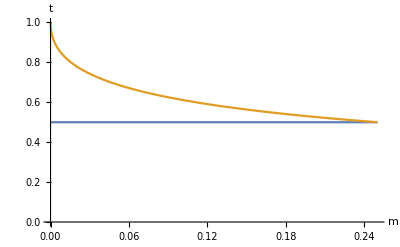

```mathematica
Clear[m,t]
Plot[{1/2,1/(1-4 m)-2 √(m/(-1+4 m)^2)},{m,0,1/4},PlotRange->{{0,.25},{0,1}},AxesLabel->{"m","t"}]
```

```mathematica
Clear[t,m]
Solve[{t==1/(1-4 m)-2 √(m/(-1+4 m)^2),m==0.05}]
```

{{m→0.05,t→0.690983}}

Mirrored equilibria 6, 7

Finally, the (mirrored) equilibria {-(1-2 t)/(t-2 m t),(-1+t+2 m t+√(1+t (-2+t-4 m t)))/(2 (-1+2 m) t),(1-(1+2 m) t+√(1+t (-2+t-4 m t)))/((2-4 m) t)},{-(1-2 t)/(t-2 m t),(1-(1+2 m) t+√(1+t (-2+t-4 m t)))/((2-4 m) t),(-1+t+2 m t+√(1+t (-2+t-4 m t)))/(2 (-1+2 m) t)}are stable when (0≤m≤1/4&&t==1/2)||(1/2<t<1&&(1-2 t+t^2)/(4 t^2)≤m≤(-1+6 t-13 t^2+12 t^3)/(2 t (-1+4 t)^2)-√((1-10 t+37 t^2-60 t^3+36 t^4)/(t (-1+4 t)^4)))||(m==0&&t==1).

We can see that the two fringe cases where t == 1/2 and t == 1 actually are special cases corresponding to other equilibria (when m == 0 and t == 1, both equilibria are equivalent to equilibrium 4; when t==1/2,0≤m≤1/4, these equilibria 6, 7 are equivalent to equilibria 2, 3):

```mathematica
Clear[t]
```

```mathematica
FullSimplify[{-(1-2 t)/(t-2 m t),(-1+t+2 m t+√(1+t (-2+t-4 m t)))/(2 (-1+2 m) t),(1-(1+2 m) t+√(1+t (-2+t-4 m t)))/((2-4 m) t)},Assumptions->{t==1/2,0≤m≤1/4}]
FullSimplify[{-(1-2 t)/(t-2 m t),(1-(1+2 m) t+√(1+t (-2+t-4 m t)))/((2-4 m) t),(-1+t+2 m t+√(1+t (-2+t-4 m t)))/(2 (-1+2 m) t)},Assumptions->{t==1/2,0≤m≤1/4}]
FullSimplify[{-(1-2 t)/(t-2 m t),(-1+t+2 m t+√(1+t (-2+t-4 m t)))/(2 (-1+2 m) t),(1-(1+2 m) t+√(1+t (-2+t-4 m t)))/((2-4 m) t)},Assumptions->{t==1,m==0}]
FullSimplify[{-(1-2 t)/(t-2 m t),(1-(1+2 m) t+√(1+t (-2+t-4 m t)))/((2-4 m) t),(-1+t+2 m t+√(1+t (-2+t-4 m t)))/(2 (-1+2 m) t)},Assumptions->{t==1,m==0}]
Clear[t]
```

{0,(-1+√(1-4 m)+2 m)/(-2+4 m),(1+√(1-4 m)-2 m)/(2-4 m)}

{0,(1+√(1-4 m)-2 m)/(2-4 m),(-1+√(1-4 m)+2 m)/(-2+4 m)}

{1,0,0}

{1,0,0}

The intermediate condition where 1/2<t<1is stable only when (1-2 t+t^2)/(4 t^2)≤m≤(-1+6 t-13 t^2+12 t^3)/(2 t (-1+4 t)^2)-√((1-10 t+37 t^2-60 t^3+36 t^4)/(t (-1+4 t)^4))...

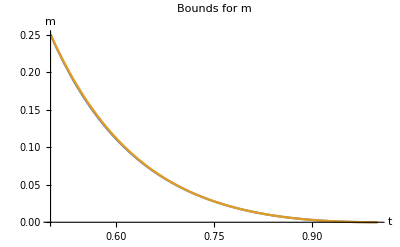

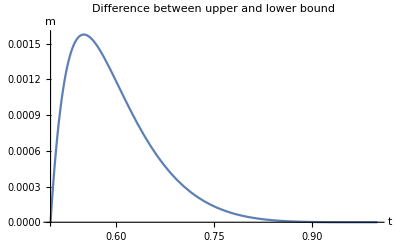

```mathematica
Plot[{(1-2 t+t^2)/(4 t^2),(-1+6 t-13 t^2+12 t^3)/(2 t (-1+4 t)^2)-√((1-10 t+37 t^2-60 t^3+36 t^4)/(t (-1+4 t)^4))},{t,1/2,1},PlotLabel->"Bounds for m",AxesLabel->{"t","m"}]
Plot[{((-1+6 t-13 t^2+12 t^3)/(2 t (-1+4 t)^2)-√((1-10 t+37 t^2-60 t^3+36 t^4)/(t (-1+4 t)^4)))-(1-2 t+t^2)/(4 t^2)},{t,1/2,1},PlotLabel->"Difference between upper and lower bound",AxesLabel->{"t","m"}]
```

Given the very small difference between the bounds, we can simplify with a simple approximation of this stability condition:

1/2<t<1; m~(1-2 t+t^2)/(4 t^2)

Seeing as this is so extremely specific, it is probably not a very realistic stable equilibrium and it seems more likely that the frequencies will tend towards some other stable equilibrium.

### Special case: m_1= m_2 = 0

#### Fixed point analysis

```mathematica
Clear[psO,pmO,pO,psA,pmA,pA,psB,pmB,pB,m,m1,m2,t,l,β];
```

```mathematica
fixedPoints={pO,pA,pB}/.FullSimplify[Solve[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},0,0,beta[t,l]]],t,l]=={pO,pA,pB},{pO,pA,pB}],Assumptions->{4 t-4 t^2≤l≤1,1/2+(√(1-l))/2≤t≤1,{pO,pA,pB,m,t,l}∈ Reals}]
```

{{(-1+2 t+√(1+(4 (-1+t) t)/l))/(2 t),0,-(-1+√(1+(4 (-1+t) t)/l))/(2 t)},{-(1-2 t+√(1+(4 (-1+t) t)/l))/(2 t),0,(1+√(1+(4 (-1+t) t)/l))/(2 t)},{(-2+3 t+√((-2+t)^2+(8 (-1+t) t)/l))/(2 t),-(-2+t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t),-(-2+t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t)},{-(2-3 t+√((-2+t)^2+(8 (-1+t) t)/l))/(2 t),(2-t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t),(2-t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t)},{(-1+2 t+√(1+(4 (-1+t) t)/l))/(2 t),-(-1+√(1+(4 (-1+t) t)/l))/(2 t),0},{-(1-2 t+√(1+(4 (-1+t) t)/l))/(2 t),(1+√(1+(4 (-1+t) t)/l))/(2 t),0},{1,0,0}}

These equilibria apparently recapitulate those presented by Turelli (1994) in his seminal paper. In fact, those equilibria are re-derived here several times, e.g.:

```mathematica
FullSimplify[(1+√(1+(4 (-1+t) t)/l))/(2 t)==1/(2t)+1/(2t)√(1-(4(1-t)t)/l),Assumptions->{0≤l≤1,0≤t≤1}]
```

True

This makes sense, given that this model essentially is the same as Turelli studied when no migration occurs.

# 3 | Asymmetric migration model with genotypes

In this version of the model, we introduce the r / R genotypes for a total of six equations.

## Defining the model

### Step 1 : Migration

```mathematica
pMigration[{pOr_,pAr_,pBr_,pOR_,pAR_,pBR_},m1_,m2_,β_]:={
(1-(m1+m2))pOr+(m1+m2)(1-β),
(1-(m1+m2))pAr+m1 β,
(1-(m1+m2))pBr+m2 β,
(1-(m1+m2))pOR,
(1-(m1+m2))pAR,
(1-(m1+m2))pBR
};
```

### Step 2 : Selection

```mathematica
pSelection[{pmOr_,pmAr_,pmBr_,pmOR_,pmAR_,pmBR_},s_]:={
pmOr/(pmOr+pmAr+pmBr+(1+s)(pmOR+pmAR+pmBR)),
pmAr/(pmOr+pmAr+pmBr+(1+s)(pmOR+pmAR+pmBR)),
pmBr/(pmOr+pmAr+pmBr+(1+s)(pmOR+pmAR+pmBR)),
((1+s) pmOR)/(pmOr+pmAr+pmBr+(1+s)(pmOR+pmAR+pmBR)),
((1+s)pmAR)/(pmOr+pmAr+pmBr+(1+s)(pmOR+pmAR+pmBR)),
((1+s)pmBR)/(pmOr+pmAr+pmBr+(1+s)(pmOR+pmAR+pmBR))
};
```

### Step 3 : Reproduction

```mathematica
pNext[{psOr_,psAr_,psBr_,psOR_,psAR_,psBR_},t_,l_,ρt_,ρl_]:={
(1/2 (-2 (-1+psAR+psBR+psOR)+t (-psAR-2 psBr-psBR+psAr (-2+psAR+psBR+psOR)+(psAR+psBr+psBR) (psAR+psBR+psOR)-(psAR+psBR) (-1+psAR+psBR+psOR) ρt)+l (-2 psBr-psBR+psBr psBR+psBR^2+psBr psOR+psBR psOR+2 psAr^2 t+2 psBr^2 t+2 psBr psBR t-psAR^2 (-1+ρl)+psBR ρl-psBR^2 ρl-psBR psOR ρl-psBr psBR t ρl-psBr psBR t ρt+psAR (psBr-(-1+2 psBR+psOR) (-1+ρl)-psBr t (-2+ρl+ρt))+psAr (-2+psAR+psBR+psOR+4 psBr t-psAR t (-2+ρl+ρt)-psBR t (-2+ρl+ρt)))))/(l (psAr^2 t+psAR (-1+ρl)+psAR^2 t (-1+ρl) (-1+ρt)-psAr (1+psAR t (-2+ρl+ρt))+(psBr+psBR-psBR ρl) (-1+t (psBr+psBR-psBR ρt)))+1),
(1/2 (-psAr t (-2+psAR+psBR+psOR+l (2 psBr+psBR-psBR ρl))+psAR (-1+psAR+l psBr+psBR+psOR) t (-1+ρt)))/(l (psAr^2 t+psAR (-1+ρl)+psAR^2 t (-1+ρl) (-1+ρt)-psAr (1+psAR t (-2+ρl+ρt))+(psBr+psBR-psBR ρl) (-1+t (psBr+psBR-psBR ρt)))+1),
(1/2 (-psBr t (-2+psAR+psBR+psOR+l (2 psAr+psAR-psAR ρl))+psBR (-1+l psAr+psAR+psBR+psOR) t (-1+ρt)))/(l (psAr^2 t+psAR (-1+ρl)+psAR^2 t (-1+ρl) (-1+ρt)-psAr (1+psAR t (-2+ρl+ρt))+(psBr+psBR-psBR ρl) (-1+t (psBr+psBR-psBR ρt)))+1),
(1/2 (2 psOR-(psAr+psBr) psOR (l+t)-psBR (-2+(1+psAr+psBr+psOR) t+l (1+psAr+psBr+psOR+psAr t (-2+ρl)+psBr t (-2+ρl)-(1+psOR) ρl))+psAR^2 (l (-1+ρl) (1+2 t (-1+ρt))+t (-1+ρt))+psBR^2 (l (-1+ρl) (1+2 t (-1+ρt))+t (-1+ρt))+psBR (1-l (psAr+psBr)+psOR) t ρt+psAR (2-(1+psAr+psBr+2 psBR+psOR) t-l (psAr+psBr+psAr t (-2+ρl)+psBr t (-2+ρl)-(1+psOR+psBR (2-4 t)) (-1+ρl))+t (1+2 psBR+psOR-l (psAr+psBr+4 psBR-4 psBR ρl)) ρt)))/(l (psAr^2 t+psAR (-1+ρl)+psAR^2 t (-1+ρl) (-1+ρt)-psAr (1+psAR t (-2+ρl+ρt))+(psBr+psBR-psBR ρl) (-1+t (psBr+psBR-psBR ρt)))+1),
(1/2 t (psAr (psBR+psOR+l psBR (-1+ρl))+psAR (psAr-(1-l psBr+psBR+psOR+2 l psBR (-1+ρl)) (-1+ρt))-psAR^2 (-1+ρt)))/(l (psAr^2 t+psAR (-1+ρl)+psAR^2 t (-1+ρl) (-1+ρt)-psAr (1+psAR t (-2+ρl+ρt))+(psBr+psBR-psBR ρl) (-1+t (psBr+psBR-psBR ρt)))+1),
(1/2 t (psBr (psAR+psOR+l psAR (-1+ρl))+psBR (psBr-(1-l psAr+psAR+psOR+2 l psAR (-1+ρl)) (-1+ρt))-psBR^2 (-1+ρt)))/(l (psAr^2 t+psAR (-1+ρl)+psAR^2 t (-1+ρl) (-1+ρt)-psAr (1+psAR t (-2+ρl+ρt))+(psBr+psBR-psBR ρl) (-1+t (psBr+psBR-psBR ρt)))+1)
};
```

### Full derivation of Step 3: Reproduction

```mathematica
Clear[t,r,ρt,ρl]
```

```mathematica
psOr=1-psAr-psBr-psOR-psAR-psBR;
```

```mathematica
CrossesReference[psOr_,psAr_,psBr_,psOR_,psAR_,psBR_]:=
(psOr*psOr)+(psOr*psAr)+(psOr*psBr)+(psOr*psOR)+(psOr*psAR)+(psOr*psBR)+
(psAr*psOr)+(psAr*psAr)+(psAr*psBr)+(psAr*psOR)+(psAr*psAR)+(psAr*psBR)+
(psBr*psOr)+(psBr*psAr)+(psBr*psBr)+(psBr*psOR)+(psBr*psAR)+(psBr*psBR)+
(psOR*psOr)+(psOR*psAr)+(psOR*psBr)+(psOR*psOR)+(psOR*psAR)+(psOR*psBR)+
(psAR*psOr)+(psAR*psAr)+(psAR*psBr)+(psAR*psOR)+(psAR*psAR)+(psAR*psBR)+
(psBR*psOr)+(psBR*psAr)+(psBR*psBr)+(psBR*psOR)+(psBR*psAR)+(psBR*psBR);
```

```mathematica
pOrNext[psOr_,psAr_,psBr_,psOR_,psAR_,psBR_,t_,l_,ρt_,ρl_]:=
(psOr*psOr)(1*1*1)+(psOr*psAr)(1*(1-l)*1)+(psOr*psBr)(1*(1-l)*1)+(psOr*psOR)(1*1*1/2)+(psOr*psAR)(1*(1-l(1-ρl))*1/2)+(psOr*psBR)(1*(1-l(1-ρl))*1/2)+
(psAr*psOr)((1-t)*1*1)+(psAr*psAr)((1-t)*(1-l)*1)+(psAr*psBr)((1-t)*(1-l)*1)+(psAr*psOR)((1-t)*1*1/2)+(psAr*psAR)((1-t)*(1-l(1-ρl))*1/2)+(psAr*psBR)((1-t)*(1-l(1-ρl))*1/2)+
(psBr*psOr)((1-t)*1*1)+(psBr*psAr)((1-t)*(1-l)*1)+(psBr*psBr)((1-t)*(1-l)*1)+(psBr*psOR)((1-t)*1*1/2)+(psBr*psAR)((1-t)*(1-l(1-ρl))*1/2)+(psBr*psBR)((1-t)*(1-l(1-ρl))*1/2)+
(psOR*psOr)(1*1*1/2)+(psOR*psAr)(1*(1-l)*1/2)+(psOR*psBr)(1*(1-l)*1/2)+(psOR*psOR)(1*1*0)+(psOR*psAR)(1*(1-l)*0)+(psOR*psBR)(1*(1-l)*0)+
(psAR*psOr)((1-t(1-ρt))*1*1/2)+(psAR*psAr)((1-t(1-ρt))*(1-l)*1/2)+(psAR*psBr)((1-t(1-ρt))*(1-l)*1/2)+(psAR*psOR)((1-t(1-ρt))*1*0)+(psAR*psAR)((1-t(1-ρt))*(1-l(1-ρl))*0)+(psAR*psBR)((1-t(1-ρt))*(1-l(1-ρl))*0)+
(psBR*psOr)((1-t(1-ρt))*1*1/2)+(psBR*psAr)((1-t(1-ρt))*(1-l)*1/2)+(psBR*psBr)((1-t(1-ρt))*(1-l)*1/2)+(psBR*psOR)((1-t(1-ρt))*1*0)+(psBR*psAR)((1-t(1-ρt))*(1-l(1-ρl))*0)+(psBR*psBR)((1-t(1-ρt))*(1-l(1-ρl))*0);
```

```mathematica
FullSimplify[pOrNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]]
```

1/2 (-2 (-1+psAR+psBR+psOR)+t (-psAR-2 psBr-psBR+psAr (-2+psAR+psBR+psOR)+(psAR+psBr+psBR) (psAR+psBR+psOR)-(psAR+psBR) (-1+psAR+psBR+psOR) ρt)+l (-2 psBr-psBR+psBr psBR+psBR^2+psBr psOR+psBR psOR+2 psAr^2 t+2 psBr^2 t+2 psBr psBR t-psAR^2 (-1+ρl)+psBR ρl-psBR^2 ρl-psBR psOR ρl-psBr psBR t ρl-psBr psBR t ρt+psAR (psBr-(-1+2 psBR+psOR) (-1+ρl)-psBr t (-2+ρl+ρt))+psAr (-2+psAR+psBR+psOR+4 psBr t-psAR t (-2+ρl+ρt)-psBR t (-2+ρl+ρt))))

```mathematica
pArNext[psOr_,psAr_,psBr_,psOR_,psAR_,psBR_,t_,l_,ρt_,ρl_]:=
(psOr*psOr)(0*1*1)+(psOr*psAr)(0*1*1)+(psOr*psBr)(0*(1-l)*1)+(psOr*psOR)(0*1*1/2)+(psOr*psAR)(0*1*1/2)+(psOr*psBR)(0*(1-l(1-ρl))*1/2)+
(psAr*psOr)(t*1*1)+(psAr*psAr)(t*1*1)+(psAr*psBr)(t*(1-l)*1)+(psAr*psOR)(t*1*1/2)+(psAr*psAR)(t*1*1/2)+(psAr*psBR)(t*(1-l(1-ρl))*1/2)+
(psBr*psOr)(0*1*1)+(psBr*psAr)(0*1*1)+(psBr*psBr)(0*(1-l)*1)+(psBr*psOR)(0*1*1/2)+(psBr*psAR)(0*1*1/2)+(psBr*psBR)(0*(1-l(1-ρl))*1/2)+
(psOR*psOr)(0*1*1/2)+(psOR*psAr)(0*1*1/2)+(psOR*psBr)(0*(1-l)*1/2)+(psOR*psOR)(0*1*0)+(psOR*psAR)(0*1*0)+(psOR*psBR)(0*(1-l(1-ρl))*0)+
(psAR*psOr)(t(1-ρt)*1*1/2)+(psAR*psAr)(t(1-ρt)*1*1/2)+(psAR*psBr)(t(1-ρt)*(1-l)*1/2)+(psAR*psOR)(t(1-ρt)*1*0)+(psAR*psAR)(t(1-ρt)*1*0)+(psAR*psBR)(t(1-ρt)*(1-l(1-ρl))*0)+
(psBR*psOr)(0*1*1/2)+(psBR*psAr)(0*1*1/2)+(psBR*psBr)(0*(1-l)*1/2)+(psBR*psOR)(0*1*0)+(psBR*psAR)(0*1*0)+(psBR*psBR)(0*(1-l(1-ρl))*0);
```

```mathematica
FullSimplify[pArNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]]
```

1/2 (-psAr t (-2+psAR+psBR+psOR+l (2 psBr+psBR-psBR ρl))+psAR (-1+psAR+l psBr+psBR+psOR) t (-1+ρt))

```mathematica
pBrNext[psOr_,psAr_,psBr_,psOR_,psAR_,psBR_,t_,l_,ρt_,ρl_]:=
(psOr*psOr)(0*1*1)+(psOr*psAr)(0*(1-l)*1)+(psOr*psBr)(0*1*1)+(psOr*psOR)(0*1*1/2)+(psOr*psAR)(0*(1-l(1-ρl))*1/2)+(psOr*psBR)(0*1*1/2)+
(psAr*psOr)(0*1*1)+(psAr*psAr)(0*(1-l)*1)+(psAr*psBr)(0*1*1)+(psAr*psOR)(0*1*1/2)+(psAr*psAR)(0*(1-l(1-ρl))*1/2)+(psAr*psBR)(0*1*1/2)+
(psBr*psOr)(t*1*1)+(psBr*psAr)(t*(1-l)*1)+(psBr*psBr)(t*1*1)+(psBr*psOR)(t*1*1/2)+(psBr*psAR)(t*(1-l(1-ρl))*1/2)+(psBr*psBR)(t*1*1/2)+
(psOR*psOr)(0*1*1/2)+(psOR*psAr)(0*(1-l)*1/2)+(psOR*psBr)(0*1*1/2)+(psOR*psOR)(0*1*0)+(psOR*psAR)(0*(1-l(1-ρl))*0)+(psOR*psBR)(0*1*0)+
(psAR*psOr)(0*1*1/2)+(psAR*psAr)(0*(1-l)*1/2)+(psAR*psBr)(0*1*1/2)+(psAR*psOR)(0*1*0)+(psAR*psAR)(0*(1-l(1-ρl))*0)+(psAR*psBR)(0*1*0)+
(psBR*psOr)(t(1-ρt)*1*1/2)+(psBR*psAr)(t(1-ρt)*(1-l)*1/2)+(psBR*psBr)(t(1-ρt)*1*1/2)+(psBR*psOR)(t(1-ρt)*1*0)+(psBR*psAR)(t(1-ρt)*(1-l(1-ρl))*0)+(psBR*psBR)(t(1-ρt)*1*0);
```

```mathematica
FullSimplify[pBrNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]]
```

1/2 (-psBr t (-2+psAR+psBR+psOR+l (2 psAr+psAR-psAR ρl))+psBR (-1+l psAr+psAR+psBR+psOR) t (-1+ρt))

```mathematica
pORNext[psOr_,psAr_,psBr_,psOR_,psAR_,psBR_,t_,l_,ρt_,ρl_]:=
(psOr*psOr)(1*1*0)+(psOr*psAr)(1*(1-l)*0)+(psOr*psBr)(1*(1-l)*0)+(psOr*psOR)(1*1*1/2)+(psOr*psAR)(1*(1-l(1-ρl))*1/2)+(psOr*psBR)(1*(1-l(1-ρl))*1/2)+
(psAr*psOr)((1-t)*1*0)+(psAr*psAr)((1-t)*(1-l)*0)+(psAr*psBr)((1-t)*(1-l)*0)+(psAr*psOR)((1-t)*1*1/2)+(psAr*psAR)((1-t)*(1-l(1-ρl))*1/2)+(psAr*psBR)((1-t)*(1-l(1-ρl))*1/2)+
(psBr*psOr)((1-t)*1*0)+(psBr*psAr)((1-t)*(1-l)*0)+(psBr*psBr)((1-t)*(1-l)*0)+(psBr*psOR)((1-t)*1*1/2)+(psBr*psAR)((1-t)*(1-l(1-ρl))*1/2)+(psBr*psBR)((1-t)*(1-l(1-ρl))*1/2)+
(psOR*psOr)(1*1*1/2)+(psOR*psAr)(1*(1-l)*1/2)+(psOR*psBr)(1*(1-l)*1/2)+(psOR*psOR)(1*1*1)+(psOR*psAR)(1*(1-l(1-ρl))*1)+(psOR*psBR)(1*(1-l(1-ρl))*1)+
(psAR*psOr)((1-t(1-ρt))*1*1/2)+(psAR*psAr)((1-t(1-ρt))*(1-l)*1/2)+(psAR*psBr)((1-t(1-ρt))*(1-l)*1/2)+(psAR*psOR)((1-t(1-ρt))*1*1)+(psAR*psAR)((1-t(1-ρt))*(1-l(1-ρl))*1)+(psAR*psBR)((1-t(1-ρt))*(1-l(1-ρl))*1)+
(psBR*psOr)((1-t(1-ρt))*1*1/2)+(psBR*psAr)((1-t(1-ρt))*(1-l)*1/2)+(psBR*psBr)((1-t(1-ρt))*(1-l)*1/2)+(psBR*psOR)((1-t(1-ρt))*1*1)+(psBR*psAR)((1-t(1-ρt))*(1-l(1-ρl))*1)+(psBR*psBR)((1-t(1-ρt))*(1-l(1-ρl))*1);
```

```mathematica
FullSimplify[pORNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]]
```

1/2 (2 psOR-(psAr+psBr) psOR (l+t)-psBR (-2+(1+psAr+psBr+psOR) t+l (1+psAr+psBr+psOR+psAr t (-2+ρl)+psBr t (-2+ρl)-(1+psOR) ρl))+psAR^2 (l (-1+ρl) (1+2 t (-1+ρt))+t (-1+ρt))+psBR^2 (l (-1+ρl) (1+2 t (-1+ρt))+t (-1+ρt))+psBR (1-l (psAr+psBr)+psOR) t ρt+psAR (2-(1+psAr+psBr+2 psBR+psOR) t-l (psAr+psBr+psAr t (-2+ρl)+psBr t (-2+ρl)-(1+psOR+psBR (2-4 t)) (-1+ρl))+t (1+2 psBR+psOR-l (psAr+psBr+4 psBR-4 psBR ρl)) ρt))

```mathematica
pARNext[psOr_,psAr_,psBr_,psOR_,psAR_,psBR_,t_,l_,ρt_,ρl_]:=
(psOr*psOr)(0*1*0)+(psOr*psAr)(0*1*0)+(psOr*psBr)(0*(1-l)*0)+(psOr*psOR)(0*1*1/2)+(psOr*psAR)(0*1*1/2)+(psOr*psBR)(0*(1-l(1-ρl))*1/2)+
(psAr*psOr)(t*1*0)+(psAr*psAr)(t*1*0)+(psAr*psBr)(t*(1-l)*0)+(psAr*psOR)(t*1*1/2)+(psAr*psAR)(t*1*1/2)+(psAr*psBR)(t*(1-l(1-ρl))*1/2)+
(psBr*psOr)(0*1*0)+(psBr*psAr)(0*1*0)+(psBr*psBr)(0*(1-l)*0)+(psBr*psOR)(0*1*1/2)+(psBr*psAR)(0*1*1/2)+(psBr*psBR)(0*(1-l(1-ρl))*1/2)+
(psOR*psOr)(0*1*1/2)+(psOR*psAr)(0*1*1/2)+(psOR*psBr)(0*(1-l)*1/2)+(psOR*psOR)(0*1*1)+(psOR*psAR)(0*1*1)+(psOR*psBR)(0*(1-l(1-ρl))*1)+
(psAR*psOr)(t(1-ρt)*1*1/2)+(psAR*psAr)(t(1-ρt)*1*1/2)+(psAR*psBr)(t(1-ρt)*(1-l)*1/2)+(psAR*psOR)(t(1-ρt)*1*1)+(psAR*psAR)(t(1-ρt)*1*1)+(psAR*psBR)(t(1-ρt)*(1-l(1-ρl))*1)+
(psBR*psOr)(0*1*1/2)+(psBR*psAr)(0*1*1/2)+(psBR*psBr)(0*(1-l)*1/2)+(psBR*psOR)(0*1*1)+(psBR*psAR)(0*1*1)+(psBR*psBR)(0*(1-l(1-ρl))*1);
```

```mathematica
FullSimplify[pARNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]]
```

1/2 t (psAr (psBR+psOR+l psBR (-1+ρl))+psAR (psAr-(1-l psBr+psBR+psOR+2 l psBR (-1+ρl)) (-1+ρt))-psAR^2 (-1+ρt))

```mathematica
pBRNext[psOr_,psAr_,psBr_,psOR_,psAR_,psBR_,t_,l_,ρt_,ρl_]:=
(psOr*psOr)(0*1*0)+(psOr*psAr)(0*(1-l)*0)+(psOr*psBr)(0*1*0)+(psOr*psOR)(0*1*1/2)+(psOr*psAR)(0*(1-l(1-ρl))*1/2)+(psOr*psBR)(0*1*1/2)+
(psAr*psOr)(0*1*0)+(psAr*psAr)(0*(1-l)*0)+(psAr*psBr)(0*1*0)+(psAr*psOR)(0*1*1/2)+(psAr*psAR)(0*(1-l(1-ρl))*1/2)+(psAr*psBR)(0*1*1/2)+
(psBr*psOr)(t*1*0)+(psBr*psAr)(t*(1-l)*0)+(psBr*psBr)(t*1*0)+(psBr*psOR)(t*1*1/2)+(psBr*psAR)(t*(1-l(1-ρl))*1/2)+(psBr*psBR)(t*1*1/2)+
(psOR*psOr)(0*1*1/2)+(psOR*psAr)(0*(1-l)*1/2)+(psOR*psBr)(0*1*1/2)+(psOR*psOR)(0*1*1)+(psOR*psAR)(0*(1-l(1-ρl))*1)+(psOR*psBR)(0*1*1)+
(psAR*psOr)(0*1*1/2)+(psAR*psAr)(0*(1-l)*1/2)+(psAR*psBr)(0*1*1/2)+(psAR*psOR)(0*1*1)+(psAR*psAR)(0*(1-l(1-ρl))*1)+(psAR*psBR)(0*1*1)+
(psBR*psOr)(t(1-ρt)*1*1/2)+(psBR*psAr)(t(1-ρt)*(1-l)*1/2)+(psBR*psBr)(t(1-ρt)*1*1/2)+(psBR*psOR)(t(1-ρt)*1*1)+(psBR*psAR)(t(1-ρt)*(1-l(1-ρl))*1)+(psBR*psBR)(t(1-ρt)*1*1);
```

```mathematica
FullSimplify[pBRNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]]
```

1/2 t (psBR+(psBr+psBR) (psBR+psOR)+psAR (psBr+l psBr (-1+ρl)-psBR (1+2 l (-1+ρl)) (-1+ρt))+l psAr psBR (-1+ρt)-psBR (1+psBR+psOR) ρt)

```mathematica
FullSimplify[1/2 t (psBR+(psBr+psBR) (psBR+psOR)+psAR (psBr+l psBr (-1+ρl)-psBR (1+2 l (-1+ρl)) (-1+ρt))+l psAr psBR (-1+ρt)-psBR (1+psBR+psOR) ρt)==1/2 t (psBr (psAR+psOR+l psAR (-1+ρl))+psBR (psBr-(1-l psAr+psAR+psOR+2 l psAR (-1+ρl)) (-1+ρt))-psBR^2 (-1+ρt))]
```

True

```mathematica
1/2 t (psBr (psAR+psOR+l psAR (-1+ρl))+psBR (psBr-(1-l psAr+psAR+psOR+2 l psAR (-1+ρl)) (-1+ρt))-psBR^2 (-1+ρt))
```

1/2 t (psBr (psAR+psOR+l psAR (-1+ρl))+psBR (psBr-(1-l psAr+psAR+psOR+2 l psAR (-1+ρl)) (-1+ρt))-psBR^2 (-1+ρt))

```mathematica
W2[psOr_,psAr_,psBr_,psOR_,psAR_,psBR_,t_,l_,ρt_,ρl_]:=FullSimplify[pOrNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]+pArNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]+pBrNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]+pORNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]+pARNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]+pBRNext[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]]
```

```mathematica
W2[psOr,psAr,psBr,psOR,psAR,psBR,t,l,ρt,ρl]
```

1+l (psAr^2 t+psAR (-1+ρl)+psAR^2 t (-1+ρl) (-1+ρt)-psAr (1+psAR t (-2+ρl+ρt))+(psBr+psBR-psBR ρl) (-1+t (psBr+psBR-psBR ρt)))

## Analytical solutions

### Special case: m_1 = m_2= 0; ρt = 0, ρl = 0; s = 0

The fixed point analysis for this most simple scenario suggests that the system cannot be meaningfully analytically solved for cases where r and R co-occur. We re-derive the Turelli-equilibria as for the asymmetric model without genotypes for scenarios where the frequency of R = 1.

#### Fixed point analysis

```mathematica
Clear[pOr,pAr,pBr,pOR,pAR,pBR,m,t,l,β,ρt,ρl,s];
```

```mathematica
fixedPoints={pOr,pAr,pBr,pOR,pAR,pBR}/.FullSimplify[Solve[pNext[pSelection[pMigration[{pOr,pAr,pBr,pOR,pAR,pBR},0,0,beta[t,l]],0],t,l,0,0]=={pOr,pAr,pBr,pOR,pAR,pBR},{pOr,pAr,pBr,pOR,pAR,pBR}],Assumptions->{4 t-4 t^2≤l≤1,1/2+(√(1-l))/2≤t≤1}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{pOr,0,0,1-pOr,0,0},{-(pBr (-2+l+2 t+√(l (l+4 (-1+t) t))))/(2 (-1+t)),0,pBr,(l^(3/2) pBr t+√l (-1+t) (-1+2 (1+pBr) t)+(-1+t) √(l+4 (-1+t) t)+l pBr t √(l+4 (-1+t) t))/(2 √l (-1+t) t),0,(l-2 l pBr t-√(l (l+4 (-1+t) t)))/(2 l t)},{(pBr (2-l-2 t+√(l (l+4 (-1+t) t))))/(2 (-1+t)),0,pBr,(l^(3/2) pBr t+√l (-1+t) (-1+2 (1+pBr) t)-(-1+t) √(l+4 (-1+t) t)-l pBr t √(l+4 (-1+t) t))/(2 √l (-1+t) t),0,(1-2 pBr t+√(1+(4 (-1+t) t)/l))/(2 t)},{-(pAr (-2+l+2 t+√(l (l+4 (-1+t) t))))/(2 (-1+t)),pAr,0,(l^(3/2) pAr t+√l (-1+t) (-1+2 (1+pAr) t)+(-1+t) √(l+4 (-1+t) t)+l pAr t √(l+4 (-1+t) t))/(2 √l (-1+t) t),(l-2 l pAr t-√(l (l+4 (-1+t) t)))/(2 l t),0},{(pAr (2-l-2 t+√(l (l+4 (-1+t) t))))/(2 (-1+t)),pAr,0,(l^(3/2) pAr t+√l (-1+t) (-1+2 (1+pAr) t)-(-1+t) √(l+4 (-1+t) t)-l pAr t √(l+4 (-1+t) t))/(2 √l (-1+t) t),(1-2 pAr t+√(1+(4 (-1+t) t)/l))/(2 t),0},{(pAr (4+l (-2+t)-4 t-√(l (l (-2+t)^2+8 (-1+t) t))))/(2 (-1+t)),pAr,pAr,(-l^(3/2) pAr (-2+t) t+√l (-1+t) (-2+(3+4 pAr) t)+(-1+t) √(l (-2+t)^2+8 (-1+t) t)+l pAr t √(l (-2+t)^2+8 (-1+t) t))/(2 √l (-1+t) t),-(-2+t+4 pAr t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t),-(-2+t+4 pAr t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t)},{(pAr (4+l (-2+t)-4 t+√(l (l (-2+t)^2+8 (-1+t) t))))/(2 (-1+t)),pAr,pAr,(-l^(3/2) pAr (-2+t) t+√l (-1+t) (-2+(3+4 pAr) t)-(-1+t) √(l (-2+t)^2+8 (-1+t) t)-l pAr t √(l (-2+t)^2+8 (-1+t) t))/(2 √l (-1+t) t),(2-(1+4 pAr) t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t),(2-(1+4 pAr) t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t)},{0,0,0,(-1+2 t+√(1+(4 (-1+t) t)/l))/(2 t),-(-1+√(1+(4 (-1+t) t)/l))/(2 t),0},{0,0,0,-(1-2 t+√(1+(4 (-1+t) t)/l))/(2 t),(1+√(1+(4 (-1+t) t)/l))/(2 t),0},{0,0,0,(-1+2 t+√(1+(4 (-1+t) t)/l))/(2 t),0,-(-1+√(1+(4 (-1+t) t)/l))/(2 t)},{0,0,0,-(1-2 t+√(1+(4 (-1+t) t)/l))/(2 t),0,(1+√(1+(4 (-1+t) t)/l))/(2 t)},{0,0,0,(-2+3 t+√((-2+t)^2+(8 (-1+t) t)/l))/(2 t),-(-2+t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t),-(-2+t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t)},{0,0,0,-(2-3 t+√((-2+t)^2+(8 (-1+t) t)/l))/(2 t),(2-t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t),(2-t+√((-2+t)^2+(8 (-1+t) t)/l))/(4 t)}}

# 4 | Numerical results

## Interactive results

Run the below cell to initialise the interactive results panel.

```mathematica
resultsInteractive[]
```

resultsInteractive[]

## Figure 2: Migration parameter space plot

NOTIFICATION: Migration space plot computed for t = 0.95  l = 0.6.

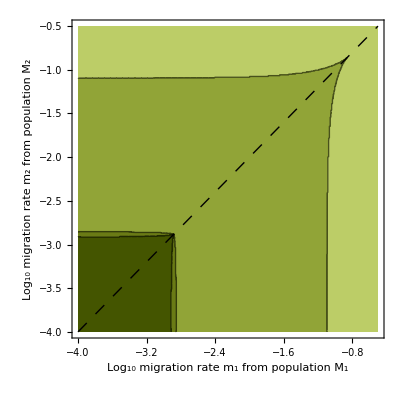

```mathematica
logMigrationSpacePlot=migrationSpacePlot[{-4,-0.5},0.95,0.6,0.035,50," "]
```

```mathematica
Export["logMigrationSpacePlot.pdf",logMigrationSpacePlot];
```

## Figure 3: Resistance equilibrium states

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.000177828 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.000316228 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.000562341 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.001 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.00177828 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.00316228 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.00562341 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.01 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.0316228 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.01 m2 = 0.0562341 t = 0.95 l = 0.6 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0316228 m2 = 0.0562341 t = 0.95 l = 0.6 ρt = 0 ρl = 1. s = 0 and returned the population state at t = 100000

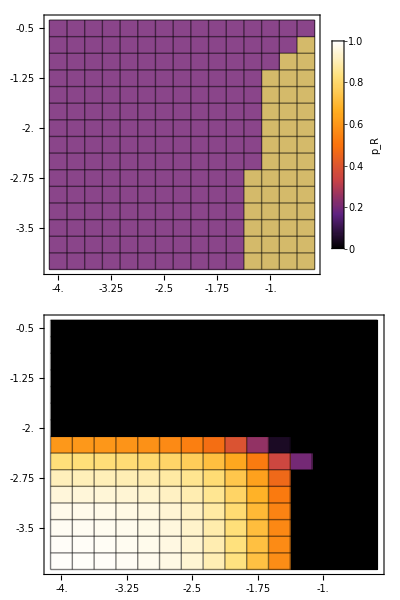
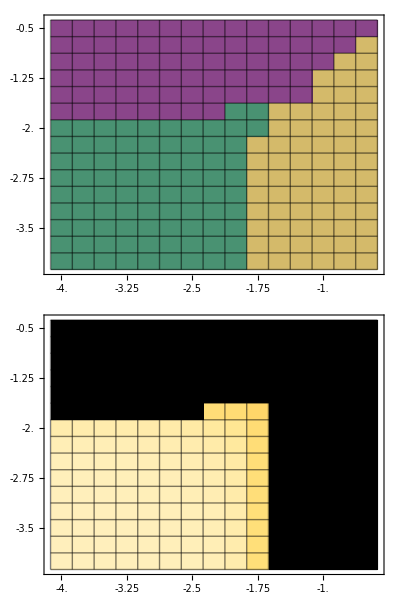
-Graphics-ρ_t = 0  ρ_l = 0.5 | -Graphics-ρ_t = 0  ρ_l = 1.Log_10 migration rate m_1 from population M_1Log_10 migration rate m_2 from population M_2

```mathematica
fig3=migrationResistancePlot[cytotypeColours,False,True,2,100000,0.001,0.001,-4.0,-0.5,0.25,0.95,0.6,{0,0},{0.5,1.0},0]
```

```mathematica
Export["resistanceEquilibriumStates.pdf",fig3];
```

## Figure 5: Barriers to spread: transmission reduction and cost of resistance

```mathematica
barrierHeatMapFigure[2,100000,0.001,0.001,{0.0015,0.015},{0.0015,0.015},0.95,0.6,Range[0,0.05,0.005],Range[1,0,-0.1],{0,-0.001}]
```

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.05 ρl = 1. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.035 ρl = 0.7 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.05 ρl = 0.7 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.03 ρl = 0.6 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.035 ρl = 0.6 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.04 ρl = 0.6 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.045 ρl = 0.6 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.05 ρl = 0.6 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.025 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.03 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.035 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.04 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.02 ρl = 0.4 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.025 ρl = 0.6 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.03 ρl = 0.6 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.035 ρl = 0.6 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.04 ρl = 0.6 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.045 ρl = 0.6 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.05 ρl = 0.6 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.03 ρl = 0.5 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.035 ρl = 0.5 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.015 ρl = 0.4 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.02 ρl = 0.4 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.025 ρl = 0.4 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.03 ρl = 0.4 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.035 ρl = 0.4 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0015 m2 = 0.0015 t = 0.95 l = 0.6 ρt = 0.04 ρl = 0.4 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.015 ρl = 1. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.02 ρl = 1. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.03 ρl = 1. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.005 ρl = 0.7 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.015 ρl = 1. s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.02 ρl = 1. s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.025 ρl = 1. s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0. ρl = 0.8 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0. ρl = 0.7 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.015 ρl = 0.6 s = -0.001 and returned the population state at t = 100000

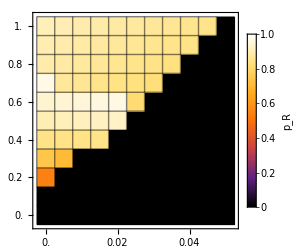
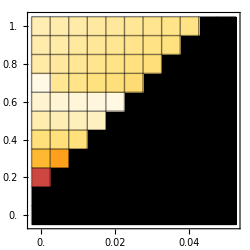
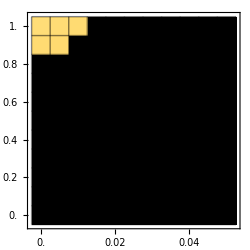
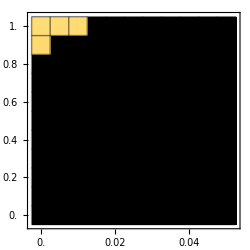
```mathematica
{{{{-Graphics-}}"s = \!\(\*RowBox[{\"0\"}]\)""", {{-Graphics-}}"s = \!\(\*RowBox[{\"-\", \"0.001`\"}]\)""\!\(\*SubscriptBox[\(m\), \(1\)]\) = \!\(\*RowBox[{\"0.0015`\"}]\)  \!\(\*SubscriptBox[\(m\), \(2\)]\) = \!\(\*RowBox[{\"0.0015`\"}]\)"}, {{{-Graphics-}}"""", {{-Graphics-}}"""\!\(\*SubscriptBox[\(m\), \(1\)]\) = \!\(\*RowBox[{\"0.015`\"}]\)  \!\(\*SubscriptBox[\(m\), \(2\)]\) = \!\(\*RowBox[{\"0.015`\"}]\)"}}"Modification rescue (\!\(\*SubscriptBox[\(ρ\), \(l\)]\))""Transmission reduction (\!\(\*SubscriptBox[\(ρ\), \(t\)]\))"
```

```mathematica
heatPlotInsets=barrierHeatMapFigure[2,100000,0.001,0.001,{0.015},{0.015},0.95,0.6,Range[0,0.015,0.0015],Range[1,0.75,-0.025],{0,-0.001}]
```

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.015 ρl = 1. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0135 ρl = 0.925 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.015 ρl = 0.925 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0105 ρl = 0.9 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.012 ρl = 0.9 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.009 ρl = 0.875 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0105 ρl = 0.875 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.006 ρl = 0.85 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0075 ρl = 0.85 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0045 ρl = 0.825 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0015 ρl = 0.775 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.003 ρl = 0.775 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0045 ρl = 0.775 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0. ρl = 0.75 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0015 ρl = 0.75 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.003 ρl = 0.75 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0045 ρl = 0.75 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.012 ρl = 1. s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.015 ρl = 1. s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.012 ρl = 0.95 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0135 ρl = 0.95 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0105 ρl = 0.925 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.012 ρl = 0.925 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0075 ρl = 0.9 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.009 ρl = 0.9 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0015 ρl = 0.875 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.006 ρl = 0.875 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0045 ρl = 0.85 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0. ρl = 0.8 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0015 ρl = 0.8 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.003 ρl = 0.8 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0. ρl = 0.775 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0015 ρl = 0.775 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.003 ρl = 0.775 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0. ρl = 0.75 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.015 m2 = 0.015 t = 0.95 l = 0.6 ρt = 0.0015 ρl = 0.75 s = -0.001 and returned the population state at t = 100000

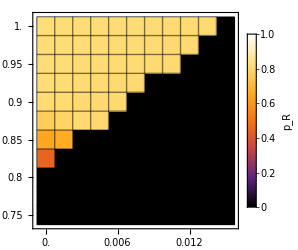
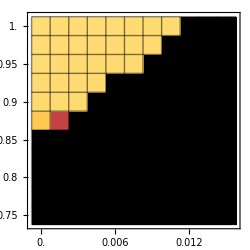
```mathematica
{{{{-Graphics-}}"s = \!\(\*RowBox[{\"0\"}]\)""", {{-Graphics-}}"s = \!\(\*RowBox[{\"-\", \"0.001`\"}]\)""\!\(\*SubscriptBox[\(m\), \(1\)]\) = \!\(\*RowBox[{\"0.015`\"}]\)  \!\(\*SubscriptBox[\(m\), \(2\)]\) = \!\(\*RowBox[{\"0.015`\"}]\)"}}"Modification rescue (\!\(\*SubscriptBox[\(ρ\), \(l\)]\))""Transmission reduction (\!\(\*SubscriptBox[\(ρ\), \(t\)]\))"
```

## Figure S2: Barriers to spread are relaxed when infection is rare

```mathematica
barrierHeatMapFigure[1,100000,0.001,0.001,{0.0001,0.001},{0.0001,0.001},0.95,0.6,Range[0,1,0.1],Range[1,0,-0.1],{0,-0.001}]
```

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.5 ρl = 0.4 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0. ρl = 0.2 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0. ρl = 0.1 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.1 ρl = 0.1 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.2 ρl = 0.1 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0. ρl = 0. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.1 ρl = 0. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.2 ρl = 0. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.3 ρl = 0. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.4 ρl = 0. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.6 ρl = 0. s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0. ρl = 1. s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.1 ρl = 1. s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.3 ρl = 1. s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.8 ρl = 0.9 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.9 ρl = 0.9 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.6 ρl = 0.8 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0. ρl = 0.7 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.1 ρl = 0.7 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.3 ρl = 0.7 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.5 ρl = 0.7 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0. ρl = 0.2 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.1 ρl = 0.2 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.7 ρl = 0.2 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 0.0001 t = 0.95 l = 0.6 ρt = 0.9 ρl = 0.2 s = -0.001 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.001 m2 = 0.001 t = 0.95 l = 0.6 ρt = 1. ρl = 1. s = -0.001 and returned the population state at t = 100000

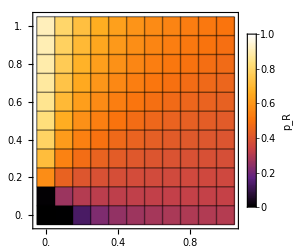
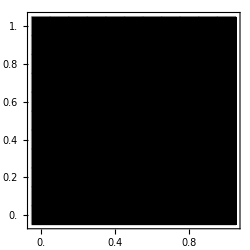
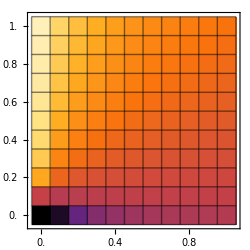
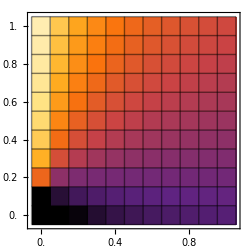
```mathematica
{{{{-Graphics-}}"s = \!\(\*RowBox[{\"0\"}]\)""", {{-Graphics-}}"s = \!\(\*RowBox[{\"-\", \"0.001`\"}]\)""\!\(\*SubscriptBox[\(m\), \(1\)]\) = \!\(\*RowBox[{\"0.0001`\"}]\)  \!\(\*SubscriptBox[\(m\), \(2\)]\) = \!\(\*RowBox[{\"0.0001`\"}]\)"}, {{{-Graphics-}}"""", {{-Graphics-}}"""\!\(\*SubscriptBox[\(m\), \(1\)]\) = \!\(\*RowBox[{\"0.001`\"}]\)  \!\(\*SubscriptBox[\(m\), \(2\)]\) = \!\(\*RowBox[{\"0.001`\"}]\)"}}"Modification rescue (\!\(\*SubscriptBox[\(ρ\), \(l\)]\))""Transmission reduction (\!\(\*SubscriptBox[\(ρ\), \(t\)]\))"
```

## Figure S3: Mosquito migration space plot

NOTIFICATION: Migration space plot computed for t = 0.99  l = 0.99.

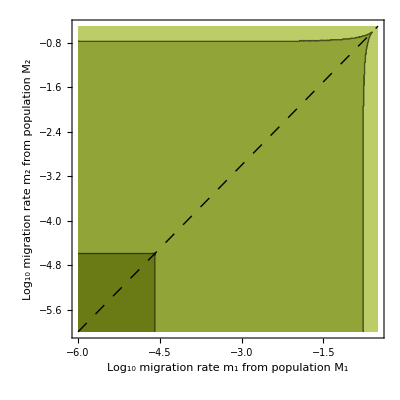

```mathematica
logMosquitoMigrationSpace=migrationSpacePlot[{-6,-0.5},0.99,0.99,0.055,50," "]
```

```mathematica
Export["mosquitoMigrationPlot.pdf",logMosquitoMigrationSpace];
```

## Figure S4: Mosquito resistance equilibrium states

WARNING: tryResistance timed out with m1 = 0.0001 m2 = 1.×10^-6 t = 0.99 l = 0.99 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.000316228 m2 = 0.00316228 t = 0.99 l = 0.99 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.00316228 m2 = 0.0001 t = 0.99 l = 0.99 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 0.00316228 m2 = 0.000316228 t = 0.99 l = 0.99 ρt = 0 ρl = 0.5 s = 0 and returned the population state at t = 100000

WARNING: tryResistance timed out with m1 = 1.×10^-6 m2 = 1.×10^-6 t = 0.99 l = 0.99 ρt = 0 ρl = 1. s = 0 and returned the population state at t = 100000

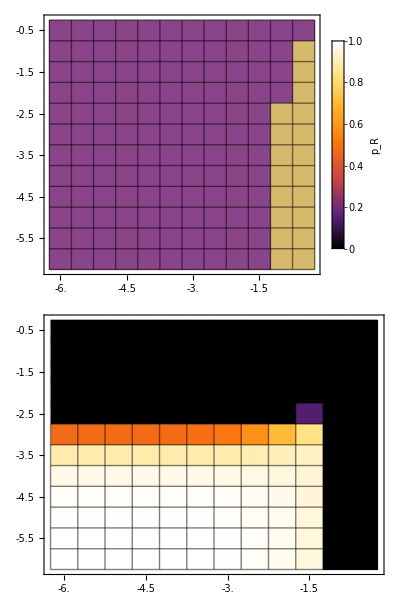
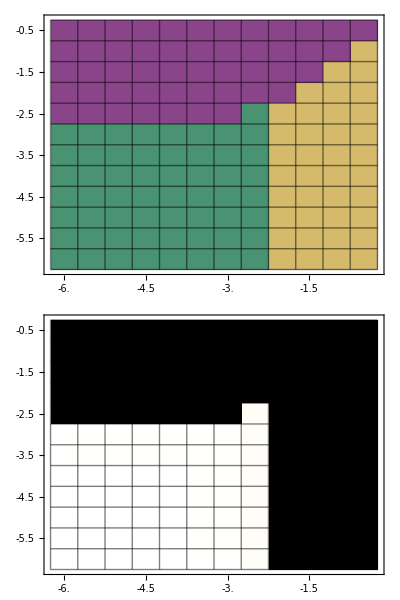
-Graphics-ρ_t = 0  ρ_l = 0.5 | -Graphics-ρ_t = 0  ρ_l = 1.Log_10 migration rate m_1 from population M_1Log_10 migration rate m_2 from population M_2

```mathematica
figS4=migrationResistancePlot[cytotypeColours,False,True,2,100000,0.001,0.001,-6.0,-0.5,0.5,0.99,0.99,{0,0},{0.5,1.0},0]
```

```mathematica
Export["mosquitoResistanceEquilibriumStates.pdf",figS4];
```

# 5 | Helper and visualisation functions

## Numerical solution functions

### Asymmetric model without genotypes

```mathematica
numericalSimpleEquilibria[m1_,m2_,t_,l_]:=(
Quiet[Cases[{pO,pA,pB}/.Solve[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},m1,m2,beta[t,l]]],t,l]=={pO,pA,pB},{pO,pA,pB}],fixed_/;
fixed[[{1,2,3}]]∈Reals&&fixed[[1]]+fixed[[2]]+fixed[[3]]==1&& 0≤fixed[[1]]≤1&&0≤fixed[[2]]≤1&&0≤fixed[[3]]≤1
]
]
)
```

```mathematica
numericalSimpleStability[m1_,m2_,t_,l_,fixedP_]:=(
Quiet[
Jacob[{pO_,pA_,pB_}]=D[pNextSimple[pSelectionSimple[pMigrationSimple[{pO,pA,pB},m1,m2,beta[t,l]]],t,l],{{pO,pA,pB}}];
eigenvalues={};
For[i=1,i≤Length[fixedP],i++,
jacobian=Jacob[fixedP⟦i⟧];
eigenvalues = Join[eigenvalues,{Eigenvalues[jacobian]}];
];
stable=Table[If[Length[Select[Abs[eigenvalues[[e]]],GreaterEqualThan[1.0]]]>0,False,True],{e,1,Length[eigenvalues]}]
]
)
```

```mathematica
numericalSimple[pO_,pA_,pB_,m1_,m2_,t_,l_,gens_]:=(
Quiet[
frequencies={{pO,pA,pB}};
For[i=1,i≤gens,i++,
frequencies=Join[frequencies,{pNextSimple[pSelectionSimple[pMigrationSimple[frequencies[[i]],m1,m2,beta[t,l]]],t,l]}];
];
frequencies
]
)
```

### Asymmetric model with genotypes

```mathematica
numericalEquilibria[m1_,m2_,t_,l_,ρt_,ρl_,s_,precision_]:=(
fixedPoints=Quiet[Cases[{pOr,pAr,pBr,pOR,pAR,pBR}/.NSolve[pNext[pSelection[pMigration[{pOr,pAr,pBr,pOR,pAR,pBR},m1,m2,beta[t,l]],s],t,l,ρt,ρl]=={pOr,pAr,pBr,pOR,pAR,pBR},{pOr,pAr,pBr,pOR,pAR,pBR},Reals],fixed_/;
fixed[[{1,2,3,4,5,6}]]∈Reals&&
Total[fixed]==1&&
0≤fixed[[1]]≤1&&
0≤fixed[[2]]≤1&&
0≤fixed[[3]]≤1&&
0≤fixed[[4]]≤1&&
0≤fixed[[5]]≤1&&
0≤fixed[[6]]≤1
]
];
If[Length[fixedPoints]==0,Print[StringForm["WARNING: No equilibria exist for m1 = `1` m2 = `2` t = `3` l = `4` ρt = `5` ρl = `6` s = `7`",m1,m2,t,l,ρt, ρl, s]],Null];
fixedPoints=N[Round[fixedPoints,precision]];
fixedPoints=DeleteDuplicates[fixedPoints]
)
```

```mathematica
numericalStability[m1_,m2_,t_,l_,ρt_,ρl_,s_,fixedP_]:=(
Quiet[
Jacob[{pOr_,pAr_,pBr_}]=D[pNext[pSelection[pMigration[{pOr,pAr,pBr,pOR,pAR,pBR},m1,m2,beta[t,l]],s],t,l,ρt,ρl],{{pOr,pAr,pBr,pOR,pAR,pBR}}];
eigenvalues={};
For[i=1,i≤Length[fixedP],i++,
jacobian=Jacob[fixedP⟦i⟧];
eigenvalues = Join[eigenvalues,{Eigenvalues[jacobian]}];
];
stable=Table[If[Length[Select[Abs[eigenvalues[[e]]],GreaterEqualThan[1.0]]]>0,False,True],{e,1,Length[eigenvalues]}]
]
)
```

```mathematica
numerical[pOr_,pAr_,pBr_,pOR_,pAR_,pBR_,m1_,m2_,t_,l_,ρt_,ρl_,s_,gens_]:=(
Quiet[
frequencies={{pOr,pAr,pBr,pOR,pAR,pBR}};
For[i=1,i≤gens,i++,
frequencies= Join[frequencies,{pNext[pSelection[pMigration[frequencies[[i]],m1,m2,beta[t,l]],s],t,l,ρt,ρl]}];
];
frequencies
]
)
```

## Frequency diagrams

### Asymmetric model without genotypes

```mathematica
frequencyPlotSimple[pO_,pA_,pB_,m1_,m2_,t_,l_,gens_,legend_]:=(

frequencies=numericalSimple[pO,pA,pB,m1,m2,t,l,gens];

ListLinePlot[
{frequencies[[Range[gens],1]],frequencies[[Range[gens],2]],frequencies[[Range[gens],3]]},
PlotStyle->{{cytotypeColours⟦1⟧,Dashing[None]},{cytotypeColours⟦2⟧,Dashing[None]},{cytotypeColours⟦3⟧,Dashing[None]}},
FrameLabel->{Style["Generation",FontFamily->"Helvetica",16], Style["Frequency",FontFamily->"Helvetica",16]},
PlotRange->{{1,gens},{-0.02,1.02}},
AspectRatio->2/GoldenRatio,
ImagePadding->{0,0};
PlotLegends->If[legend==True,{Style["p_O",FontFamily->"Times",22],Style["p_A",FontFamily->"Times",22],Style["p_B",FontFamily->"Times",22]},{}],
PlotTheme->{"Monochrome","Helvetica"},
PlotMarkers->None,
Frame->True,
ImageSize->300]
)
```

### Asymmetric model with genotypes

```mathematica
frequencyPlot[pOr_,pAr_,pBr_,pOR_,pAR_,pBR_,m1_,m2_,t_,l_,ρt_,ρl_,s_,gens_,overviewTF_]:=(

frequencies=numerical[pOr,pAr,pBr,pOR,pAR,pBR,m1,m2,t,l,ρt,ρl,s,gens];

mainPanel=ListLinePlot[
{frequencies[[Range[gens],1]],frequencies[[Range[gens],2]],frequencies[[Range[gens],3]],frequencies[[Range[gens],4]],frequencies[[Range[gens],5]],frequencies[[Range[gens],6]]},
PlotStyle->{{cytotypeColours⟦1⟧,Dashing[None]},{cytotypeColours⟦2⟧,Dashing[None]},{cytotypeColours⟦3⟧,Dashing[None]},{cytotypeColours⟦1⟧,Dashing[Medium]},{cytotypeColours⟦2⟧,Dashing[Medium]},{cytotypeColours⟦3⟧,Dashing[Medium]}},
FrameLabel->{If[overviewTF,Style[" ",FontFamily->"Times",2.5],Style["Generation",FontFamily->"Helvetica",16]], Style[" ",FontFamily->"Times",2]},
PlotRange->{{1,gens},{-0.02,1.02}},
AspectRatio->1/If[overviewTF,(1.50N[GoldenRatio]),GoldenRatio],
ImagePadding->{{0,0},{0,10}};
PlotTheme->{"Monochrome","Helvetica"},
PlotMarkers->None,
Frame->True,
ImageSize->If[overviewTF,530,530]];

frequencyLegend=PointLegend[
{cytotypeColours⟦1⟧,cytotypeColours⟦2⟧,cytotypeColours⟦3⟧,Black,Black},
{"O","A","B", "R","r"},
LegendMarkerSize->22.5,
LegendMarkers->Table[Graphics[{Thickness[0.15],Dashing[{None,None,None,Medium,None}⟦d⟧],Line[{{-1,0},{1,0}}]}],{d,1,5}],
LabelStyle->{FontFamily-> "Helvetica",FontSize->12,Black},
LegendLayout->frequencyLegendFunction
];

frequencyLegendFunction[pairs_]:=
Grid[{
{TableForm[
pairs⟦{1,2,3}⟧,
TableHeadings->{None,{Text[Style["Cyto",FontFamily->"Helvetica",FontSize->14,Black]],Text[Style["type",FontFamily->"Helvetica",FontSize->14,Black]]}},
TableAlignments->Center,
TableSpacing->{0.5,0}
]},
{TableForm[
pairs⟦{4,5}⟧,
TableHeadings->{None,{Text[Style["Geno",FontFamily->"Helvetica",FontSize->14,Black]],Text[Style["type",FontFamily->"Helvetica",FontSize->14,Black]]}},
TableAlignments->Center,
TableSpacing->{0.5,0}
]
}
},
Spacings->{0,1.5}
];

If[overviewTF,
Legended[
Grid[{
{mainPanel},
{ListLinePlot[
{
frequencies[[Range[gens],1]]+frequencies[[Range[gens],2]]+frequencies[[Range[gens],3]],
frequencies[[Range[gens],4]]+frequencies[[Range[gens],5]]+frequencies[[Range[gens],6]]
},
PlotStyle->{{Black,Dashing[None]},{Black,Dashing[Medium]}},
FrameLabel->{Style["Generation",FontFamily->"Helvetica",16], Style[" ",FontFamily->"Times",2]},
PlotRange->{{1,gens},{-0.05,1.05}},
AspectRatio->1/(4N[GoldenRatio]),
PlotTheme->{"Monochrome","Helvetica"},
PlotMarkers->None,
Frame->True,
ImageSize->530
]}
}],
frequencyLegend
],
Legended[mainPanel,frequencyLegend]
]

)
```

## Logarithmic migration parameter space plot

```mathematica
migrationSpacePlot[log10mRange_,t_,l_,searchResolution_,plotPoints_,plotLabel_]:=(

Clear[m1,m2,mRangeIter,allCounts];

allCounts={1};
mRangeIter=log10mRange/searchResolution;

For[m1=mRangeIter[[1]],m1≤mRangeIter[[2]],m1++,
For[m2=mRangeIter[[1]],m2≤mRangeIter[[2]],m2++,
equilibriumCount=Length[numericalSimpleEquilibria[10^(m1*searchResolution),10^(m2*searchResolution),t,l]];
If[MemberQ[allCounts,equilibriumCount],Null,allCounts=Join[allCounts,{equilibriumCount}]];
];
];

allCounts=Sort[allCounts];

contourPlot=ContourPlot[
Length[numericalSimpleEquilibria[10^m1,10^m2,t,l]],
{m1,log10mRange[[1]],log10mRange[[2]]},
{m2,log10mRange[[1]],log10mRange[[2]]},
Contours->Table[N[Mean[{allCounts[[e-1]],allCounts[[e]]}]],{e,2,Length[allCounts]}],
ContourShading->{RGBColor[0.737,0.804,0.404],RGBColor[0.569,0.643,0.216],RGBColor[0.416,0.482,0.082],RGBColor[0.267,0.332,0]},
ContourLabels->None,
PlotLabel->Style[plotLabel,Black,FontFamily->"Helvetica",16,FontSlant->Plain],
Frame->True,
PlotRangePadding->0,
FrameTicks->Automatic,
FrameStyle->Directive[Thin,Black],
FrameTicksStyle->Directive[Black],
FrameLabel->{Style["Log_10 migration rate m_1 from population M_1",FontFamily->"Helvetica",16], Style["Log_10 migration rate m_2 from population M_2",FontFamily->"Helvetica",16]},
PerformanceGoal->"Quality",
PlotPoints->plotPoints,
ImageSize->400
];

Print[StringForm["NOTIFICATION: Migration space plot computed for t = `1`  l = `2`.",t,l]];
Show[contourPlot,Graphics[{Dashing[Medium],Line[{{log10mRange[[1]],log10mRange[[1]]},{log10mRange[[2]],log10mRange[[2]]}}]}]]

)
```

## de Finetti diagrams

```mathematica
ternaryToCartesian[a_,b_,c_]:={1/2(2b+c)/(a+b+c),(√3)/2 c/(a+b+c)};
```

```mathematica
deFinetti[labels_,paths_,equilibria_,stable_,hlpTF_,highlightPath_]:=
Quiet[
Graphics[
{

{
EdgeForm[Thickness[0.0025]],White,Simplex[{{0,0},{1/2,(√3)/2},{1,0}}]
},

Text[Style[labels[[1]],cytotypeColours⟦1⟧,FontFamily->"Times",FontSize->28,FontSlant->Italic],{-0.05,-0.05}],
Text[Style[labels[[2]],cytotypeColours⟦2⟧,FontFamily->"Times",FontSize->28,FontSlant->Italic],{1.05,-0.05}],
Text[Style[labels[[3]],cytotypeColours⟦3⟧,FontFamily->"Times",FontSize->28,FontSlant->Italic],{1/2,(√3)/2+0.08}],

pL=Null; (* path length i.e. number of generations *)
allPoints={};
allColours={};

For[a=1,a≤Length[paths],a++,
path=paths[[a]];
cartesianPath=path;
pL=Length[cartesianPath]; (* Assuming all paths of same length *)
allColours=Join[allColours,Table[ColorData["BlueGreenYellow"][g],{g,0,1.5,1.5/(pL-1)}]];
For[b=1,b≤Length[path],b++,
point = path[[b]];
cartesianPoint=ternaryToCartesian[point[[1]],point[[2]],point[[3]]];
cartesianPath[[b]]=cartesianPoint;
];
allPoints=Join[allPoints,cartesianPath];
];

If[hlpTF,
highlightCartesian=highlightPath;
For[h = 1,h≤Length[highlightPath],h++,
point=highlightPath⟦h⟧;
cartesianPoint=ternaryToCartesian[(point⟦1⟧+point⟦4⟧),(point⟦2⟧+point⟦5⟧),(point⟦3⟧+point⟦6⟧)];
highlightCartesian⟦h⟧=cartesianPoint;
],
Null
];

Table[{Dashing[Tiny],Gray,Line[allPoints[[Range[(1+c*pL),(pL + c*pL)]]]]},{c,0,Length[paths]-1}],
Table[{allColours[[p]], PointSize[0.015],Point[allPoints[[p]]]},{p,1,Length[allPoints],1}],

If[hlpTF,
{{Red,Thickness[0.0075],Arrowheads[{{0,0},{0.05,0.2},{0.05,0.4},{0.05,0.6},{0.05,0.8},{0,1}}],Arrow[highlightCartesian]},
{Red,EdgeForm[{Thickness[0.0035],Black}],Disk[highlightCartesian⟦Length[highlightCartesian]⟧,0.03]}},
Null
],

equilibriaCartesian=Table[ternaryToCartesian[equilibria[[e]][[1]],equilibria[[e]][[2]],equilibria[[e]][[3]]],{e,1,Length[equilibria]}];
Table[{EdgeForm[{Thickness[0.0035],If[stable[[e]],White,Black]}],If[stable[[e]],Black,White],Opacity[1],Disk[equilibriaCartesian[[e]],0.03]},{e,1,Length[equilibriaCartesian],1}],
Table[Text[Style[e,FontFamily->"Helvetica",FontSize->14,If[stable[[e]],White,Black]],equilibriaCartesian[[e]],{0,0.1}],{e,1,Length[equilibriaCartesian],1}]

},

ImageSize->Medium

]
]
```

## Resistance evolution analysis

```mathematica
tryResistance[pO_,pA_,pB_,pRinit_,m1_,m2_,t_,l_,ρt_,ρl_,s_,timeOut_,precision_]:=
(
allEquilibria=numericalEquilibria[m1,m2,t,l,ρt,ρl,s,precision];
stable=numericalStability[m1,m2,t,l,ρt,ρl,s,allEquilibria];
stableEquilibria=Table[If[stable[[equilibrium]]==True,N[Round[allEquilibria[[equilibrium]],precision]],Nothing],{equilibrium,Length[stable]}];

freqs={{pO(1-pRinit),pA(1-pRinit),pB(1-pRinit),pO pRinit,pA pRinit,pB pRinit}};

Quiet[
For[i=2,i≤timeOut,i++,
freqs=Join[freqs,{pNext[pSelection[pMigration[freqs[[i-1]],m1,m2,beta[t,l]],s],t,l,ρt,ρl]}];
(* when timeout is reached, return results from current generation as if it were an equilibrium and notify *)
If[i==timeOut,Print[StringForm["WARNING: tryResistance timed out with m1 = `1` m2 = `2` t = `3` l = `4` ρt = `5` ρl = `6` s = `7` and returned the population state at t = `8`", m1,m2,t,l,ρt,ρl,s,i]];Goto[returnResult],Continue];
If[MemberQ[stableEquilibria,N[Round[freqs[[i]],precision]]],Goto[returnResult],Continue];
];
];

Label[returnResult];
Return[{
Sum[freqs[[i]][[a]],{a,4,6}],
Sum[freqs[[i]][[b]],{b,{1,4}}],
freqs[[i]][[4]],
Sum[freqs[[i]][[b]],{b,{2,5}}],
freqs[[i]][[5]],
Sum[freqs[[i]][[b]],{b,{3,6}}],
freqs[[i]][[6]],
i
}] (* return: {pR, pO, pOR, pA, pAR, pB, pBR, t} *)
)
```

### Resistance equilibrium state screen

```mathematica
migrationResistanceScreen[colours_,blendTF_,pRPlot_,axisLabels_,paramLabel_,initDominant_,timeOut_,precision_,pRinit_,log10mMin_,log10mMax_,log10mResolution_,t_,l_,ρt_,ρl_,s_]:=
(* initDominant = 1 for O, 2 for A, 3 for B*)
(
log10mVals=Range[log10mMin,log10mMax,log10mResolution];
resultsMatrix={}; (* Empty matrix *)
If[pRPlot,pRMatrix={},Null];

(* Note: y and x are actually inverted here, by accident. m1 is on the x axis and m2 on the y axis. This is reversed during plotting. *)
For[x=1,x≤Length[log10mVals],x++,

resultsMatrix=Join[resultsMatrix,{{}}]; (* Add row *)
If[pRPlot,pRMatrix=Join[pRMatrix,{{}}],Null];

For[y=1,y≤Length[log10mVals],y++,

(* Find the equilibrium in which cytotype initDominant is dominant *)
equilibria=numericalSimpleEquilibria[10^log10mVals⟦x⟧,10^log10mVals⟦y⟧,t,l];
equilibrium=Table[If[equilibria⟦i2⟧⟦initDominant⟧==Max[Table[equilibria⟦i1⟧⟦initDominant⟧,{i1,Length[equilibria]}]],equilibria⟦i2⟧,Nothing],{i2,Length[equilibria]}]⟦1⟧;
solution=tryResistance[equilibrium⟦1⟧,equilibrium⟦2⟧,equilibrium⟦3⟧,pRinit,10^log10mVals⟦x⟧,10^log10mVals⟦y⟧,t,l,ρt,ρl,s,timeOut,precision];

If[pRPlot,pRMatrix⟦x⟧=Append[pRMatrix⟦x⟧,solution⟦1⟧],Null];
If[blendTF,
(* if blend, blend colours *)
colourBlock=Blend[{colours⟦1⟧,colours⟦2⟧,colours⟦3⟧},{solution⟦2⟧,solution⟦4⟧,solution⟦6⟧}],
(* else one colour*)
dominantO=If[solution⟦2⟧==Max[solution⟦Range[2,6,2]⟧],True,False];
dominantA=If[solution⟦4⟧==Max[solution⟦Range[2,6,2]⟧],True,False];
dominantB=If[solution⟦6⟧==Max[solution⟦Range[2,6,2]⟧],True,False];
colourBlock=Which[dominantO,colours⟦1⟧,dominantA,colours⟦2⟧,dominantB,colours⟦3⟧];
];

resultsMatrix⟦x⟧=Append[resultsMatrix⟦x⟧,colourBlock] (* Add element in current column to row *)

];

];

Labeled[
Grid[{
{
MatrixPlot[Reverse[resultsMatrix],PlotRangePadding->None,ImagePadding->{{35,5},{35,15}},
FrameTicks->{{Table[{y,ToString[Reverse[log10mVals]⟦y⟧]},{y,Length[log10mVals]}],None},{Table[{x,Rotate[ToString[log10mVals⟦x⟧],90 Degree]},{x,Length[log10mVals]}],None}}, (* y = m1, x = m2*)
Mesh->All,MeshStyle->Directive[Black,Opacity[0.5]],FrameStyle->Black,
ImageSize->250,
FrameLabel->If[axisLabels,{Text[Style["m_1",FontFamily->"Helvetica",FontSize->14,Black,TextAlignment->Center]],Text[Style["m_2",FontFamily->"Helvetica",FontSize->14,Black,TextAlignment->Center]]},None]]
},
If[pRPlot,
{MatrixPlot[Reverse[pRMatrix],PlotRangePadding->None,ImagePadding->{{35,5},{35,5}},
ColorFunctionScaling->False,
ColorFunction->"SunsetColors",
FrameTicks->{{Table[{y,ToString[Reverse[log10mVals]⟦y⟧]},{y,Length[log10mVals]}],None},{Table[{x,Rotate[ToString[log10mVals⟦x⟧],90 Degree]},{x,Length[log10mVals]}],None}}, (* y = m1, x = m2 *)
Mesh->All,MeshStyle->Directive[Black,Opacity[0.5]],FrameStyle->Black,
ImageSize->250,
FrameLabel->If[axisLabels,{Text[Style["m_1",FontFamily->"Helvetica",FontSize->14,Black,TextAlignment->Center]],Text[Style["m_2",FontFamily->"Helvetica",FontSize->14,Black,TextAlignment->Center]]},None]]
},
{}
]
},
Spacings->{1, 1}],
Text[Style[paramLabel,FontFamily->"Helvetica",14,TextAlignment->Right]],Top
]
)
```

```mathematica
migrationResistancePlot[colours_,blendTF_,pRPlot_,initDominant_,timeOut_,precision_,pRinit_,log10mMin_,log10mMax_,log10mResolution_,t_,l_,ρtVals_,ρlVals_,s_]:=
(
Labeled[
Legended[
Grid[
{
Table[migrationResistanceScreen[colours,blendTF,pRPlot,False,StringForm["ρ_t = `1`  ρ_l = `2`",ρtVals⟦a⟧,ρlVals⟦a⟧],initDominant,timeOut,precision,pRinit,log10mMin,log10mMax,log10mResolution,t,l,ρtVals⟦a⟧,ρlVals⟦a⟧,s],{a,1,Length[ρtVals]}]
},
Spacings->{0.5, 0.5}
],
BarLegend[{"SunsetColors",{0,1}},LegendLabel->Text[Style["p_R",FontFamily->"Helvetica",16]]]
],
{Text[Style["Log_10 migration rate m_1 from population M_1",FontFamily->"Helvetica",16]],Text[Style["Log_10 migration rate m_2 from population M_2",FontFamily->"Helvetica",16]]},
{Left,Bottom},RotateLabel->True
]
)
```

### Barriers to resistance heat plots

```mathematica
barrierHeatMap[initDominant_,timeOut_,precision_,pRinit_,m1_,m2_,t_,l_,ρtVals_,ρlVals_,s_]:=
(
equilibria=numericalSimpleEquilibria[m1,m2,t,l];
equilibrium=Table[If[equilibria⟦i2⟧⟦initDominant⟧==Max[Table[equilibria⟦i1⟧⟦initDominant⟧,{i1,Length[equilibria]}]],equilibria⟦i2⟧,Nothing],{i2,Length[equilibria]}]⟦1⟧;

pRMatrix={};
For[ρl=1,ρl≤Length[ρlVals],ρl++,
pRMatrix=Join[pRMatrix,{{}}];
For[ρt=1,ρt≤Length[ρtVals],ρt++,
solution=tryResistance[equilibrium⟦1⟧,equilibrium⟦2⟧,equilibrium⟦3⟧,pRinit,m1,m2,t,l,ρtVals⟦ρt⟧,ρlVals⟦ρl⟧,s,timeOut,precision];
pRMatrix⟦ρl⟧=Append[pRMatrix⟦ρl⟧,solution⟦1⟧];
];
];

Grid[
{{
MatrixPlot[
pRMatrix,
PlotRangePadding->None,
ImagePadding->{{35,5},{35,5}},
ColorFunctionScaling->False,
ColorFunction->"SunsetColors",
FrameTicks->{{Table[{ρl,ToString[ρlVals⟦ρl⟧]},{ρl,Length[ρlVals]}],None},{Table[{ρt,Rotate[ToString[ρtVals⟦ρt⟧],90 Degree]},{ρt,Length[ρtVals]}],None}},
Mesh->All,
MeshStyle->Directive[Black,Opacity[0.5]],
FrameStyle->Black,
ImageSize->250
]
}},
Spacings->{0,0}
]

)
```

```mathematica
barrierHeatMapFigure[initDominant_,timeOut_,precision_,pRinit_,m1Vals_,m2Vals_,t_,l_,ρtVals_,ρlVals_,sVals_]:=
(
Legended[
Labeled[
Grid[
Table[
Table[
Labeled[
barrierHeatMap[initDominant,timeOut,precision,pRinit,m1Vals⟦m⟧,m2Vals⟦m⟧,t,l,ρtVals,ρlVals,sVals⟦s⟧],
{
If[m==1,Text[Style[StringForm["s = `1`",sVals⟦s⟧],FontFamily->"Helvetica",FontSize->14]],""],
If[s==Length[sVals],Text[Style[StringForm["m_1 = `1`  m_2 = `2`",m1Vals⟦m⟧,m2Vals⟦m⟧],FontFamily->"Helvetica",FontSize->14]],""]
},
{Top,Right},
RotateLabel->True
],
{s,Length[sVals]}
],
{m,Length[m1Vals]}
],
Spacings->{-1,-1}
],
{Text[Style["Modification rescue (ρ_l)",FontFamily->"Helvetica",FontSize->16]],Text[Style["Transmission reduction (ρ_t)",FontFamily->"Helvetica",FontSize->16]]},
{Left,Bottom},
RotateLabel->True
],
BarLegend[{"SunsetColors",{0,1}},LegendLabel->Text[Style["p_R",FontFamily->"Helvetica",16]]]
]
)
```

## Interactive diagram

```mathematica
resultsInteractive[]:=
(
Clear[m1,m2,t,l,pO,pA,pB,pOr,pAr,pBr,pOR,pAR,pBR,generationsSimple,generationsResistance,selectedInitCondition,currentEquilibria,equilibriumChoice,validEquilibrium,restrictParametersTF,overviewPlotsTF,lineRTF];
Quiet[
Manipulate[
currentEquilibria=numericalSimpleEquilibria[m1,m2,t,l];
validEquilibrium=If[equilibriumChoice>Length[currentEquilibria],Length[currentEquilibria],equilibriumChoice];
interGrid=Grid[{{
dF=deFinetti[
{"p_O","p_A","p_B"},
{
numericalSimple[1,0,0,m1,m2,t,l,generationsSimple],
numericalSimple[0,1,0,m1,m2,t,l,generationsSimple],
numericalSimple[0,0,1,m1,m2,t,l,generationsSimple],
numericalSimple[0.5,0.5,0,m1,m2,t,l,generationsSimple],
numericalSimple[0.5,0,0.5,m1,m2,t,l,generationsSimple],
numericalSimple[0,0.5,0.5,m1,m2,t,l,generationsSimple],
numericalSimple[0.75,0.25,0,m1,m2,t,l,generationsSimple],
numericalSimple[0.75,0,0.25,m1,m2,t,l,generationsSimple],
numericalSimple[0.25,0.75,0,m1,m2,t,l,generationsSimple],
numericalSimple[0.25,0,0.75,m1,m2,t,l,generationsSimple],
numericalSimple[0,0.25,0.75,m1,m2,t,l,generationsSimple],
numericalSimple[0,0.75,0.25,m1,m2,t,l,generationsSimple]
},
currentEquilibria,
numericalSimpleStability[m1,m2,t,l,currentEquilibria],
showRedLine,
numerical[
currentEquilibria[[validEquilibrium]][[1]]-pOR*currentEquilibria[[validEquilibrium]][[1]],
currentEquilibria[[validEquilibrium]][[2]]-pAR*currentEquilibria[[validEquilibrium]][[2]],
currentEquilibria[[validEquilibrium]][[3]]-pBR*currentEquilibria[[validEquilibrium]][[3]],
pOR*currentEquilibria[[validEquilibrium]][[1]],
pAR*currentEquilibria[[validEquilibrium]][[2]],
pBR*currentEquilibria[[validEquilibrium]][[3]],
m1,m2,t,l,ρt,ρl,s,generationsResistance
]
],
fPS=frequencyPlotSimple[selectedInitCondition[[1]],selectedInitCondition[[2]],selectedInitCondition[[3]],m1,m2,t,l,generationsSimple,False],
fP=frequencyPlot[
currentEquilibria[[validEquilibrium]][[1]]-pOR*currentEquilibria[[validEquilibrium]][[1]],
currentEquilibria[[validEquilibrium]][[2]]-pAR*currentEquilibria[[validEquilibrium]][[2]],
currentEquilibria[[validEquilibrium]][[3]]-pBR*currentEquilibria[[validEquilibrium]][[3]],
pOR*currentEquilibria[[validEquilibrium]][[1]],
pAR*currentEquilibria[[validEquilibrium]][[2]],
pBR*currentEquilibria[[validEquilibrium]][[3]],
m1,m2,t,l,ρt,ρl,s,generationsResistance,overviewPlotsTF]}
}],
Item[Style["General settings",12],Alignment->Center],
Item[Style[" "]],
{{m1,0.05,"Migration from mainland 1 (m_1)"},0,If[restrictParametersTF,0.15,1-m2],0.0005},
{{m2,0.05,"Migration from mainland 2 (m_2)"},0,If[restrictParametersTF,0.15,1-m1],0.0005},
{{t,0.95, "Transmission rate (t)"},If[restrictParametersTF,0.90,1/2+(√(1-l))/2+0.0000001],1,0.01},
{{l,0.60, "CI level (l)"},If[restrictParametersTF,0.4,4 t-4 t^2+0.0000001],1,0.01},
{{restrictParametersTF, True,"Restrict to realistic settings"},{True,False}},
Item[Style[" "]],
Item[Style[" "]],
Item[Style["Simplified model settings",12],Alignment->Center],
Item[Style[" "]],
{{selectedInitCondition,{0.75,0,0.25},"Track initial frequencies {p_O,p_A,p_B}: "},
{
{1,0,0},{0,1,0},{0,0,1},{0.5,0.5,0},{0.5,0,0.5},{0,0.5,0.5},{0.75,0.25,0},{0.75,0,0.25},{0.25,0.75,0},{0.25,0,0.75},{0,0.25,0.75},{0,0.75,0.25}
},
ControlType->PopupMenu},
{{generationsSimple,50,"Generations"},10,1000,10},
Item[Style[" "]],
Item[Style[" "]],
Item[Style["Resistance model settings",12],Alignment->Center],
Item[Style[" "]],
{{equilibriumChoice,1,"Start from simple model equilibrium: "},
Range[1,Length[numericalSimpleEquilibria[m1,m2,t,l]]],
ControlType->SetterBar},
{{s,0,"Selection coefficient for R (s)"},-1,1,0.01},
{{ρt,0,"Transmission reduction (ρt)"},0,1,0.01},
{{ρl,1,"Modification rescue (ρl)"},0,1,0.01},
{{pOR,0.001,"Fraction of p_Or mutating to p_OR"},0,1,0.001},
{{pAR,0.001,"Fraction of p_Ar mutating to p_AR"},0,1,0.001},
{{pBR,0.001,"Fraction of p_Br mutating to p_BR"},0,1,0.001},
{{generationsResistance,1500,"Generations"},10,2500,10},
{{overviewPlotsTF, True,"Show allele frequency plot "},{True,False}},
{{showRedLine,False,"Show resistance de Finetti path"},{True,False}},
Item[Style[" "]],
Item[Style[" "]],
Button["Export all panels to PDF",Export[ToString[StringForm["m1 = `1` m2 = `2` t = `3` l = `4` s = `5` rho_t = `6` rho_l = `7` all panels.pdf",m1,m2,t,l,s,ρt,ρl]],interGrid]],
Button["Export de Finetti diagram to PDF",Export[ToString[StringForm["m1 = `1` m2 = `2` t = `3` l = `4` s = `5` rho_t = `6` rho_l = `7` de Finetti.pdf",m1,m2,t,l,s,ρt,ρl]],dF]],
Button["Export frequency plots to PDF",Export[ToString[StringForm["m1 = `1` m2 = `2` t = `3` l = `4` s = `5` rho_t = `6` rho_l = `7` frequency plots.pdf",m1,m2,t,l,s,ρt,ρl]],Grid[{{fPS,fP}}]]],
ControlPlacement->Left,
AppearanceElements->All
]
]
)
```